```mathematica
(*Mathematica*)
```

```mathematica
(* from binary Represenation of edges of the Dodecahedron:Marc Bellon Elements of dodecahedral cosmology*)
```

```mathematica
p[x_]=x^30-522*x^25-10005*x^20-10005*x^10+522*x^5+1
```

1+522 x^5-10005 x^10-10005 x^20-522 x^25+x^30

```mathematica
(*using the 2d and 3d roots as Killing vectors to construct a Cartan-Graham matrix*)
```

```mathematica
(* 2d Complex killing vectors*)
```

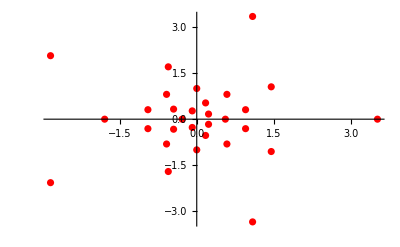

```mathematica
ki={Re[x],Im[x]}/.NSolve[p[x]==0,x];
ListPlot[%,PlotStyle->Red]
```

```mathematica
pts={2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[p[x]==0,x];
```

```mathematica
(2*ki.Transpose[ki]/12.391435051850296)//Chop
```

{{2.,0.618034,0.824429,0.54035,0.333955,0.54035,0,0.824429,-0.314904,0.316769,0.097887,0.130577,0.130577,-0.0498759,0.333955,-0.333955,0.097887,-0.256271,-0.0498759,-0.161402,-0.256271,0,-0.54035,-0.333955,-0.54035,0.618034,-1.61803,-0.314904,-1.01905,-1.61803},{0.618034,2.,0.824429,0.333955,0.54035,0,0.54035,-0.314904,0.824429,0.097887,0.316769,0.130577,-0.0498759,0.130577,-0.333955,0.333955,-0.256271,0.097887,-0.161402,-0.0498759,-0.256271,-0.54035,0,-0.54035,-0.333955,-1.61803,0.618034,-1.01905,-0.314904,-1.61803},{0.824429,0.824429,0.519232,0.275322,0.275322,0.170159,0.170159,0.160452,0.160452,0.130577,0.130577,0.0822383,0.025413,0.025413,0,0,-0.0498759,-0.0498759,-0.0665322,-0.0665322,-0.161402,-0.170159,-0.170159,-0.275322,-0.275322,-0.314904,-0.314904,-0.420068,-0.420068,-1.01905},{0.54035,0.333955,0.275322,0.161402,0.130577,0.130577,0.0498759,0.170159,0,0.0855831,0.0528933,0.0436068,0.0269505,0,0.0498759,-0.0498759,0,-0.0528933,-0.0269505,-0.0436068,-0.0855831,-0.0498759,-0.130577,-0.130577,-0.161402,0,-0.333955,-0.170159,-0.275322,-0.54035},{0.333955,0.54035,0.275322,0.130577,0.161402,0.0498759,0.130577,0,0.170159,0.0528933,0.0855831,0.0436068,0,0.0269505,-0.0498759,0.0498759,-0.0528933,0,-0.0436068,-0.0269505,-0.0855831,-0.130577,-0.0498759,-0.161402,-0.130577,-0.333955,0,-0.275322,-0.170159,-0.54035},{0.54035,0,0.170159,0.130577,0.0498759,0.161402,-0.0498759,0.275322,-0.170159,0.0855831,0,0.0269505,0.0436068,-0.0269505,0.130577,-0.130577,0.0528933,-0.0855831,0,-0.0436068,-0.0528933,0.0498759,-0.161402,-0.0498759,-0.130577,0.333955,-0.54035,0,-0.275322,-0.333955},{0,0.54035,0.170159,0.0498759,0.130577,-0.0498759,0.161402,-0.170159,0.275322,0,0.0855831,0.0269505,-0.0269505,0.0436068,-0.130577,0.130577,-0.0855831,0.0528933,-0.0436068,0,-0.0528933,-0.161402,0.0498759,-0.130577,-0.0498759,-0.54035,0.333955,-0.275322,0,-0.333955},{0.824429,-0.314904,0.160452,0.170159,0,0.275322,-0.170159,0.519232,-0.420068,0.130577,-0.0498759,0.025413,0.0822383,-0.0665322,0.275322,-0.275322,0.130577,-0.161402,0.025413,-0.0665322,-0.0498759,0.170159,-0.275322,0,-0.170159,0.824429,-1.01905,0.160452,-0.420068,-0.314904},{-0.314904,0.824429,0.160452,0,0.170159,-0.170159,0.275322,-0.420068,0.519232,-0.0498759,0.130577,0.025413,-0.0665322,0.0822383,-0.275322,0.275322,-0.161402,0.130577,-0.0665322,0.025413,-0.0498759,-0.275322,0.170159,-0.170159,0,-1.01905,0.824429,-0.420068,0.160452,-0.314904},{0.316769,0.097887,0.130577,0.0855831,0.0528933,0.0855831,0,0.130577,-0.0498759,0.0501713,0.0155038,0.0206813,0.0206813,-0.00789957,0.0528933,-0.0528933,0.0155038,-0.0405894,-0.00789957,-0.0255635,-0.0405894,0,-0.0855831,-0.0528933,-0.0855831,0.097887,-0.256271,-0.0498759,-0.161402,-0.256271},{0.097887,0.316769,0.130577,0.0528933,0.0855831,0,0.0855831,-0.0498759,0.130577,0.0155038,0.0501713,0.0206813,-0.00789957,0.0206813,-0.0528933,0.0528933,-0.0405894,0.0155038,-0.0255635,-0.00789957,-0.0405894,-0.0855831,0,-0.0855831,-0.0528933,-0.256271,0.097887,-0.161402,-0.0498759,-0.256271},{0.130577,0.130577,0.0822383,0.0436068,0.0436068,0.0269505,0.0269505,0.025413,0.025413,0.0206813,0.0206813,0.0130253,0.00402503,0.00402503,0,0,-0.00789957,-0.00789957,-0.0105377,-0.0105377,-0.0255635,-0.0269505,-0.0269505,-0.0436068,-0.0436068,-0.0498759,-0.0498759,-0.0665322,-0.0665322,-0.161402},{0.130577,-0.0498759,0.025413,0.0269505,0,0.0436068,-0.0269505,0.0822383,-0.0665322,0.0206813,-0.00789957,0.00402503,0.0130253,-0.0105377,0.0436068,-0.0436068,0.0206813,-0.0255635,0.00402503,-0.0105377,-0.00789957,0.0269505,-0.0436068,0,-0.0269505,0.130577,-0.161402,0.025413,-0.0665322,-0.0498759},{-0.0498759,0.130577,0.025413,0,0.0269505,-0.0269505,0.0436068,-0.0665322,0.0822383,-0.00789957,0.0206813,0.00402503,-0.0105377,0.0130253,-0.0436068,0.0436068,-0.0255635,0.0206813,-0.0105377,0.00402503,-0.00789957,-0.0436068,0.0269505,-0.0269505,0,-0.161402,0.130577,-0.0665322,0.025413,-0.0498759},{0.333955,-0.333955,0,0.0498759,-0.0498759,0.130577,-0.130577,0.275322,-0.275322,0.0528933,-0.0528933,0,0.0436068,-0.0436068,0.161402,-0.161402,0.0855831,-0.0855831,0.0269505,-0.0269505,0,0.130577,-0.130577,0.0498759,-0.0498759,0.54035,-0.54035,0.170159,-0.170159,0},{-0.333955,0.333955,0,-0.0498759,0.0498759,-0.130577,0.130577,-0.275322,0.275322,-0.0528933,0.0528933,0,-0.0436068,0.0436068,-0.161402,0.161402,-0.0855831,0.0855831,-0.0269505,0.0269505,0,-0.130577,0.130577,-0.0498759,0.0498759,-0.54035,0.54035,-0.170159,0.170159,0},{0.097887,-0.256271,-0.0498759,0,-0.0528933,0.0528933,-0.0855831,0.130577,-0.161402,0.0155038,-0.0405894,-0.00789957,0.0206813,-0.0255635,0.0855831,-0.0855831,0.0501713,-0.0405894,0.0206813,-0.00789957,0.0155038,0.0855831,-0.0528933,0.0528933,0,0.316769,-0.256271,0.130577,-0.0498759,0.097887},{-0.256271,0.097887,-0.0498759,-0.0528933,0,-0.0855831,0.0528933,-0.161402,0.130577,-0.0405894,0.0155038,-0.00789957,-0.0255635,0.0206813,-0.0855831,0.0855831,-0.0405894,0.0501713,-0.00789957,0.0206813,0.0155038,-0.0528933,0.0855831,0,0.0528933,-0.256271,0.316769,-0.0498759,0.130577,0.097887},{-0.0498759,-0.161402,-0.0665322,-0.0269505,-0.0436068,0,-0.0436068,0.025413,-0.0665322,-0.00789957,-0.0255635,-0.0105377,0.00402503,-0.0105377,0.0269505,-0.0269505,0.0206813,-0.00789957,0.0130253,0.00402503,0.0206813,0.0436068,0,0.0436068,0.0269505,0.130577,-0.0498759,0.0822383,0.025413,0.130577},{-0.161402,-0.0498759,-0.0665322,-0.0436068,-0.0269505,-0.0436068,0,-0.0665322,0.025413,-0.0255635,-0.00789957,-0.0105377,-0.0105377,0.00402503,-0.0269505,0.0269505,-0.00789957,0.0206813,0.00402503,0.0130253,0.0206813,0,0.0436068,0.0269505,0.0436068,-0.0498759,0.130577,0.025413,0.0822383,0.130577},{-0.256271,-0.256271,-0.161402,-0.0855831,-0.0855831,-0.0528933,-0.0528933,-0.0498759,-0.0498759,-0.0405894,-0.0405894,-0.0255635,-0.00789957,-0.00789957,0,0,0.0155038,0.0155038,0.0206813,0.0206813,0.0501713,0.0528933,0.0528933,0.0855831,0.0855831,0.097887,0.097887,0.130577,0.130577,0.316769},{0,-0.54035,-0.170159,-0.0498759,-0.130577,0.0498759,-0.161402,0.170159,-0.275322,0,-0.0855831,-0.0269505,0.0269505,-0.0436068,0.130577,-0.130577,0.0855831,-0.0528933,0.0436068,0,0.0528933,0.161402,-0.0498759,0.130577,0.0498759,0.54035,-0.333955,0.275322,0,0.333955},{-0.54035,0,-0.170159,-0.130577,-0.0498759,-0.161402,0.0498759,-0.275322,0.170159,-0.0855831,0,-0.0269505,-0.0436068,0.0269505,-0.130577,0.130577,-0.0528933,0.0855831,0,0.0436068,0.0528933,-0.0498759,0.161402,0.0498759,0.130577,-0.333955,0.54035,0,0.275322,0.333955},{-0.333955,-0.54035,-0.275322,-0.130577,-0.161402,-0.0498759,-0.130577,0,-0.170159,-0.0528933,-0.0855831,-0.0436068,0,-0.0269505,0.0498759,-0.0498759,0.0528933,0,0.0436068,0.0269505,0.0855831,0.130577,0.0498759,0.161402,0.130577,0.333955,0,0.275322,0.170159,0.54035},{-0.54035,-0.333955,-0.275322,-0.161402,-0.130577,-0.130577,-0.0498759,-0.170159,0,-0.0855831,-0.0528933,-0.0436068,-0.0269505,0,-0.0498759,0.0498759,0,0.0528933,0.0269505,0.0436068,0.0855831,0.0498759,0.130577,0.130577,0.161402,0,0.333955,0.170159,0.275322,0.54035},{0.618034,-1.61803,-0.314904,0,-0.333955,0.333955,-0.54035,0.824429,-1.01905,0.097887,-0.256271,-0.0498759,0.130577,-0.161402,0.54035,-0.54035,0.316769,-0.256271,0.130577,-0.0498759,0.097887,0.54035,-0.333955,0.333955,0,2.,-1.61803,0.824429,-0.314904,0.618034},{-1.61803,0.618034,-0.314904,-0.333955,0,-0.54035,0.333955,-1.01905,0.824429,-0.256271,0.097887,-0.0498759,-0.161402,0.130577,-0.54035,0.54035,-0.256271,0.316769,-0.0498759,0.130577,0.097887,-0.333955,0.54035,0,0.333955,-1.61803,2.,-0.314904,0.824429,0.618034},{-0.314904,-1.01905,-0.420068,-0.170159,-0.275322,0,-0.275322,0.160452,-0.420068,-0.0498759,-0.161402,-0.0665322,0.025413,-0.0665322,0.170159,-0.170159,0.130577,-0.0498759,0.0822383,0.025413,0.130577,0.275322,0,0.275322,0.170159,0.824429,-0.314904,0.519232,0.160452,0.824429},{-1.01905,-0.314904,-0.420068,-0.275322,-0.170159,-0.275322,0,-0.420068,0.160452,-0.161402,-0.0498759,-0.0665322,-0.0665322,0.025413,-0.170159,0.170159,-0.0498759,0.130577,0.025413,0.0822383,0.130577,0,0.275322,0.170159,0.275322,-0.314904,0.824429,0.160452,0.519232,0.824429},{-1.61803,-1.61803,-1.01905,-0.54035,-0.54035,-0.333955,-0.333955,-0.314904,-0.314904,-0.256271,-0.256271,-0.161402,-0.0498759,-0.0498759,0,0,0.097887,0.097887,0.130577,0.130577,0.316769,0.333955,0.333955,0.54035,0.54035,0.618034,0.618034,0.824429,0.824429,2.}}

```mathematica
Transpose[ki].ki
```

{{45.,0.},{0.,45.}}

```mathematica
ca=Table[2*ki[[i]].ki[[j]]/(ki[[i]].ki[[i]]),{i,Length[ki]},{j,Length[ki]}]//Chop
```

{{2.,0.618034,0.824429,0.54035,0.333955,0.54035,0,0.824429,-0.314904,0.316769,0.097887,0.130577,0.130577,-0.0498759,0.333955,-0.333955,0.097887,-0.256271,-0.0498759,-0.161402,-0.256271,0,-0.54035,-0.333955,-0.54035,0.618034,-1.61803,-0.314904,-1.01905,-1.61803},{0.618034,2.,0.824429,0.333955,0.54035,0,0.54035,-0.314904,0.824429,0.097887,0.316769,0.130577,-0.0498759,0.130577,-0.333955,0.333955,-0.256271,0.097887,-0.161402,-0.0498759,-0.256271,-0.54035,0,-0.54035,-0.333955,-1.61803,0.618034,-1.01905,-0.314904,-1.61803},{3.17557,3.17557,2.,1.0605,1.0605,0.655423,0.655423,0.618034,0.618034,0.502961,0.502961,0.316769,0.097887,0.097887,0,0,-0.192114,-0.192114,-0.256271,-0.256271,-0.621694,-0.655423,-0.655423,-1.0605,-1.0605,-1.21296,-1.21296,-1.61803,-1.61803,-3.92522},{6.69572,4.13818,3.41164,2.,1.61803,1.61803,0.618034,2.10851,0,1.0605,0.655423,0.54035,0.333955,0,0.618034,-0.618034,0,-0.655423,-0.333955,-0.54035,-1.0605,-0.618034,-1.61803,-1.61803,-2.,0,-4.13818,-2.10851,-3.41164,-6.69572},{4.13818,6.69572,3.41164,1.61803,2.,0.618034,1.61803,0,2.10851,0.655423,1.0605,0.54035,0,0.333955,-0.618034,0.618034,-0.655423,0,-0.54035,-0.333955,-1.0605,-1.61803,-0.618034,-2.,-1.61803,-4.13818,0,-3.41164,-2.10851,-6.69572},{6.69572,0,2.10851,1.61803,0.618034,2.,-0.618034,3.41164,-2.10851,1.0605,0,0.333955,0.54035,-0.333955,1.61803,-1.61803,0.655423,-1.0605,0,-0.54035,-0.655423,0.618034,-2.,-0.618034,-1.61803,4.13818,-6.69572,0,-3.41164,-4.13818},{0,6.69572,2.10851,0.618034,1.61803,-0.618034,2.,-2.10851,3.41164,0,1.0605,0.333955,-0.333955,0.54035,-1.61803,1.61803,-1.0605,0.655423,-0.54035,0,-0.655423,-2.,0.618034,-1.61803,-0.618034,-6.69572,4.13818,-3.41164,0,-4.13818},{3.17557,-1.21296,0.618034,0.655423,0,1.0605,-0.655423,2.,-1.61803,0.502961,-0.192114,0.097887,0.316769,-0.256271,1.0605,-1.0605,0.502961,-0.621694,0.097887,-0.256271,-0.192114,0.655423,-1.0605,0,-0.655423,3.17557,-3.92522,0.618034,-1.61803,-1.21296},{-1.21296,3.17557,0.618034,0,0.655423,-0.655423,1.0605,-1.61803,2.,-0.192114,0.502961,0.097887,-0.256271,0.316769,-1.0605,1.0605,-0.621694,0.502961,-0.256271,0.097887,-0.192114,-1.0605,0.655423,-0.655423,0,-3.92522,3.17557,-1.61803,0.618034,-1.21296},{12.6275,3.90211,5.20524,3.41164,2.10851,3.41164,0,5.20524,-1.98823,2.,0.618034,0.824429,0.824429,-0.314904,2.10851,-2.10851,0.618034,-1.61803,-0.314904,-1.01905,-1.61803,0,-3.41164,-2.10851,-3.41164,3.90211,-10.2159,-1.98823,-6.43403,-10.2159},{3.90211,12.6275,5.20524,2.10851,3.41164,0,3.41164,-1.98823,5.20524,0.618034,2.,0.824429,-0.314904,0.824429,-2.10851,2.10851,-1.61803,0.618034,-1.01905,-0.314904,-1.61803,-3.41164,0,-3.41164,-2.10851,-10.2159,3.90211,-6.43403,-1.98823,-10.2159},{20.0498,20.0498,12.6275,6.69572,6.69572,4.13818,4.13818,3.90211,3.90211,3.17557,3.17557,2.,0.618034,0.618034,0,0,-1.21296,-1.21296,-1.61803,-1.61803,-3.92522,-4.13818,-4.13818,-6.69572,-6.69572,-7.65833,-7.65833,-10.2159,-10.2159,-24.7829},{20.0498,-7.65833,3.90211,4.13818,0,6.69572,-4.13818,12.6275,-10.2159,3.17557,-1.21296,0.618034,2.,-1.61803,6.69572,-6.69572,3.17557,-3.92522,0.618034,-1.61803,-1.21296,4.13818,-6.69572,0,-4.13818,20.0498,-24.7829,3.90211,-10.2159,-7.65833},{-7.65833,20.0498,3.90211,0,4.13818,-4.13818,6.69572,-10.2159,12.6275,-1.21296,3.17557,0.618034,-1.61803,2.,-6.69572,6.69572,-3.92522,3.17557,-1.61803,0.618034,-1.21296,-6.69572,4.13818,-4.13818,0,-24.7829,20.0498,-10.2159,3.90211,-7.65833},{4.13818,-4.13818,0,0.618034,-0.618034,1.61803,-1.61803,3.41164,-3.41164,0.655423,-0.655423,0,0.54035,-0.54035,2.,-2.,1.0605,-1.0605,0.333955,-0.333955,0,1.61803,-1.61803,0.618034,-0.618034,6.69572,-6.69572,2.10851,-2.10851,0},{-4.13818,4.13818,0,-0.618034,0.618034,-1.61803,1.61803,-3.41164,3.41164,-0.655423,0.655423,0,-0.54035,0.54035,-2.,2.,-1.0605,1.0605,-0.333955,0.333955,0,-1.61803,1.61803,-0.618034,0.618034,-6.69572,6.69572,-2.10851,2.10851,0},{3.90211,-10.2159,-1.98823,0,-2.10851,2.10851,-3.41164,5.20524,-6.43403,0.618034,-1.61803,-0.314904,0.824429,-1.01905,3.41164,-3.41164,2.,-1.61803,0.824429,-0.314904,0.618034,3.41164,-2.10851,2.10851,0,12.6275,-10.2159,5.20524,-1.98823,3.90211},{-10.2159,3.90211,-1.98823,-2.10851,0,-3.41164,2.10851,-6.43403,5.20524,-1.61803,0.618034,-0.314904,-1.01905,0.824429,-3.41164,3.41164,-1.61803,2.,-0.314904,0.824429,0.618034,-2.10851,3.41164,0,2.10851,-10.2159,12.6275,-1.98823,5.20524,3.90211},{-7.65833,-24.7829,-10.2159,-4.13818,-6.69572,0,-6.69572,3.90211,-10.2159,-1.21296,-3.92522,-1.61803,0.618034,-1.61803,4.13818,-4.13818,3.17557,-1.21296,2.,0.618034,3.17557,6.69572,0,6.69572,4.13818,20.0498,-7.65833,12.6275,3.90211,20.0498},{-24.7829,-7.65833,-10.2159,-6.69572,-4.13818,-6.69572,0,-10.2159,3.90211,-3.92522,-1.21296,-1.61803,-1.61803,0.618034,-4.13818,4.13818,-1.21296,3.17557,0.618034,2.,3.17557,0,6.69572,4.13818,6.69572,-7.65833,20.0498,3.90211,12.6275,20.0498},{-10.2159,-10.2159,-6.43403,-3.41164,-3.41164,-2.10851,-2.10851,-1.98823,-1.98823,-1.61803,-1.61803,-1.01905,-0.314904,-0.314904,0,0,0.618034,0.618034,0.824429,0.824429,2.,2.10851,2.10851,3.41164,3.41164,3.90211,3.90211,5.20524,5.20524,12.6275},{0,-6.69572,-2.10851,-0.618034,-1.61803,0.618034,-2.,2.10851,-3.41164,0,-1.0605,-0.333955,0.333955,-0.54035,1.61803,-1.61803,1.0605,-0.655423,0.54035,0,0.655423,2.,-0.618034,1.61803,0.618034,6.69572,-4.13818,3.41164,0,4.13818},{-6.69572,0,-2.10851,-1.61803,-0.618034,-2.,0.618034,-3.41164,2.10851,-1.0605,0,-0.333955,-0.54035,0.333955,-1.61803,1.61803,-0.655423,1.0605,0,0.54035,0.655423,-0.618034,2.,0.618034,1.61803,-4.13818,6.69572,0,3.41164,4.13818},{-4.13818,-6.69572,-3.41164,-1.61803,-2.,-0.618034,-1.61803,0,-2.10851,-0.655423,-1.0605,-0.54035,0,-0.333955,0.618034,-0.618034,0.655423,0,0.54035,0.333955,1.0605,1.61803,0.618034,2.,1.61803,4.13818,0,3.41164,2.10851,6.69572},{-6.69572,-4.13818,-3.41164,-2.,-1.61803,-1.61803,-0.618034,-2.10851,0,-1.0605,-0.655423,-0.54035,-0.333955,0,-0.618034,0.618034,0,0.655423,0.333955,0.54035,1.0605,0.618034,1.61803,1.61803,2.,0,4.13818,2.10851,3.41164,6.69572},{0.618034,-1.61803,-0.314904,0,-0.333955,0.333955,-0.54035,0.824429,-1.01905,0.097887,-0.256271,-0.0498759,0.130577,-0.161402,0.54035,-0.54035,0.316769,-0.256271,0.130577,-0.0498759,0.097887,0.54035,-0.333955,0.333955,0,2.,-1.61803,0.824429,-0.314904,0.618034},{-1.61803,0.618034,-0.314904,-0.333955,0,-0.54035,0.333955,-1.01905,0.824429,-0.256271,0.097887,-0.0498759,-0.161402,0.130577,-0.54035,0.54035,-0.256271,0.316769,-0.0498759,0.130577,0.097887,-0.333955,0.54035,0,0.333955,-1.61803,2.,-0.314904,0.824429,0.618034},{-1.21296,-3.92522,-1.61803,-0.655423,-1.0605,0,-1.0605,0.618034,-1.61803,-0.192114,-0.621694,-0.256271,0.097887,-0.256271,0.655423,-0.655423,0.502961,-0.192114,0.316769,0.097887,0.502961,1.0605,0,1.0605,0.655423,3.17557,-1.21296,2.,0.618034,3.17557},{-3.92522,-1.21296,-1.61803,-1.0605,-0.655423,-1.0605,0,-1.61803,0.618034,-0.621694,-0.192114,-0.256271,-0.256271,0.097887,-0.655423,0.655423,-0.192114,0.502961,0.097887,0.316769,0.502961,0,1.0605,0.655423,1.0605,-1.21296,3.17557,0.618034,2.,3.17557},{-1.61803,-1.61803,-1.01905,-0.54035,-0.54035,-0.333955,-0.333955,-0.314904,-0.314904,-0.256271,-0.256271,-0.161402,-0.0498759,-0.0498759,0,0,0.097887,0.097887,0.130577,0.130577,0.316769,0.333955,0.333955,0.54035,0.54035,0.618034,0.618034,0.824429,0.824429,2.}}

```mathematica
g1=WeightedAdjacencyGraph[ca,ImageSize->2000,EdgeStyle->Cyan,VertexStyle->Purple];
```

```mathematica
TableForm[ca]
```

2. | 0.618034 | 0.824429 | 0.54035 | 0.333955 | 0.54035 | 0 | 0.824429 | -0.314904 | 0.316769 | 0.097887 | 0.130577 | 0.130577 | -0.0498759 | 0.333955 | -0.333955 | 0.097887 | -0.256271 | -0.0498759 | -0.161402 | -0.256271 | 0 | -0.54035 | -0.333955 | -0.54035 | 0.618034 | -1.61803 | -0.314904 | -1.01905 | -1.61803
0.618034 | 2. | 0.824429 | 0.333955 | 0.54035 | 0 | 0.54035 | -0.314904 | 0.824429 | 0.097887 | 0.316769 | 0.130577 | -0.0498759 | 0.130577 | -0.333955 | 0.333955 | -0.256271 | 0.097887 | -0.161402 | -0.0498759 | -0.256271 | -0.54035 | 0 | -0.54035 | -0.333955 | -1.61803 | 0.618034 | -1.01905 | -0.314904 | -1.61803
3.17557 | 3.17557 | 2. | 1.0605 | 1.0605 | 0.655423 | 0.655423 | 0.618034 | 0.618034 | 0.502961 | 0.502961 | 0.316769 | 0.097887 | 0.097887 | 0 | 0 | -0.192114 | -0.192114 | -0.256271 | -0.256271 | -0.621694 | -0.655423 | -0.655423 | -1.0605 | -1.0605 | -1.21296 | -1.21296 | -1.61803 | -1.61803 | -3.92522
6.69572 | 4.13818 | 3.41164 | 2. | 1.61803 | 1.61803 | 0.618034 | 2.10851 | 0 | 1.0605 | 0.655423 | 0.54035 | 0.333955 | 0 | 0.618034 | -0.618034 | 0 | -0.655423 | -0.333955 | -0.54035 | -1.0605 | -0.618034 | -1.61803 | -1.61803 | -2. | 0 | -4.13818 | -2.10851 | -3.41164 | -6.69572
4.13818 | 6.69572 | 3.41164 | 1.61803 | 2. | 0.618034 | 1.61803 | 0 | 2.10851 | 0.655423 | 1.0605 | 0.54035 | 0 | 0.333955 | -0.618034 | 0.618034 | -0.655423 | 0 | -0.54035 | -0.333955 | -1.0605 | -1.61803 | -0.618034 | -2. | -1.61803 | -4.13818 | 0 | -3.41164 | -2.10851 | -6.69572
6.69572 | 0 | 2.10851 | 1.61803 | 0.618034 | 2. | -0.618034 | 3.41164 | -2.10851 | 1.0605 | 0 | 0.333955 | 0.54035 | -0.333955 | 1.61803 | -1.61803 | 0.655423 | -1.0605 | 0 | -0.54035 | -0.655423 | 0.618034 | -2. | -0.618034 | -1.61803 | 4.13818 | -6.69572 | 0 | -3.41164 | -4.13818
0 | 6.69572 | 2.10851 | 0.618034 | 1.61803 | -0.618034 | 2. | -2.10851 | 3.41164 | 0 | 1.0605 | 0.333955 | -0.333955 | 0.54035 | -1.61803 | 1.61803 | -1.0605 | 0.655423 | -0.54035 | 0 | -0.655423 | -2. | 0.618034 | -1.61803 | -0.618034 | -6.69572 | 4.13818 | -3.41164 | 0 | -4.13818
3.17557 | -1.21296 | 0.618034 | 0.655423 | 0 | 1.0605 | -0.655423 | 2. | -1.61803 | 0.502961 | -0.192114 | 0.097887 | 0.316769 | -0.256271 | 1.0605 | -1.0605 | 0.502961 | -0.621694 | 0.097887 | -0.256271 | -0.192114 | 0.655423 | -1.0605 | 0 | -0.655423 | 3.17557 | -3.92522 | 0.618034 | -1.61803 | -1.21296
-1.21296 | 3.17557 | 0.618034 | 0 | 0.655423 | -0.655423 | 1.0605 | -1.61803 | 2. | -0.192114 | 0.502961 | 0.097887 | -0.256271 | 0.316769 | -1.0605 | 1.0605 | -0.621694 | 0.502961 | -0.256271 | 0.097887 | -0.192114 | -1.0605 | 0.655423 | -0.655423 | 0 | -3.92522 | 3.17557 | -1.61803 | 0.618034 | -1.21296
12.6275 | 3.90211 | 5.20524 | 3.41164 | 2.10851 | 3.41164 | 0 | 5.20524 | -1.98823 | 2. | 0.618034 | 0.824429 | 0.824429 | -0.314904 | 2.10851 | -2.10851 | 0.618034 | -1.61803 | -0.314904 | -1.01905 | -1.61803 | 0 | -3.41164 | -2.10851 | -3.41164 | 3.90211 | -10.2159 | -1.98823 | -6.43403 | -10.2159
3.90211 | 12.6275 | 5.20524 | 2.10851 | 3.41164 | 0 | 3.41164 | -1.98823 | 5.20524 | 0.618034 | 2. | 0.824429 | -0.314904 | 0.824429 | -2.10851 | 2.10851 | -1.61803 | 0.618034 | -1.01905 | -0.314904 | -1.61803 | -3.41164 | 0 | -3.41164 | -2.10851 | -10.2159 | 3.90211 | -6.43403 | -1.98823 | -10.2159
20.0498 | 20.0498 | 12.6275 | 6.69572 | 6.69572 | 4.13818 | 4.13818 | 3.90211 | 3.90211 | 3.17557 | 3.17557 | 2. | 0.618034 | 0.618034 | 0 | 0 | -1.21296 | -1.21296 | -1.61803 | -1.61803 | -3.92522 | -4.13818 | -4.13818 | -6.69572 | -6.69572 | -7.65833 | -7.65833 | -10.2159 | -10.2159 | -24.7829
20.0498 | -7.65833 | 3.90211 | 4.13818 | 0 | 6.69572 | -4.13818 | 12.6275 | -10.2159 | 3.17557 | -1.21296 | 0.618034 | 2. | -1.61803 | 6.69572 | -6.69572 | 3.17557 | -3.92522 | 0.618034 | -1.61803 | -1.21296 | 4.13818 | -6.69572 | 0 | -4.13818 | 20.0498 | -24.7829 | 3.90211 | -10.2159 | -7.65833
-7.65833 | 20.0498 | 3.90211 | 0 | 4.13818 | -4.13818 | 6.69572 | -10.2159 | 12.6275 | -1.21296 | 3.17557 | 0.618034 | -1.61803 | 2. | -6.69572 | 6.69572 | -3.92522 | 3.17557 | -1.61803 | 0.618034 | -1.21296 | -6.69572 | 4.13818 | -4.13818 | 0 | -24.7829 | 20.0498 | -10.2159 | 3.90211 | -7.65833
4.13818 | -4.13818 | 0 | 0.618034 | -0.618034 | 1.61803 | -1.61803 | 3.41164 | -3.41164 | 0.655423 | -0.655423 | 0 | 0.54035 | -0.54035 | 2. | -2. | 1.0605 | -1.0605 | 0.333955 | -0.333955 | 0 | 1.61803 | -1.61803 | 0.618034 | -0.618034 | 6.69572 | -6.69572 | 2.10851 | -2.10851 | 0
-4.13818 | 4.13818 | 0 | -0.618034 | 0.618034 | -1.61803 | 1.61803 | -3.41164 | 3.41164 | -0.655423 | 0.655423 | 0 | -0.54035 | 0.54035 | -2. | 2. | -1.0605 | 1.0605 | -0.333955 | 0.333955 | 0 | -1.61803 | 1.61803 | -0.618034 | 0.618034 | -6.69572 | 6.69572 | -2.10851 | 2.10851 | 0
3.90211 | -10.2159 | -1.98823 | 0 | -2.10851 | 2.10851 | -3.41164 | 5.20524 | -6.43403 | 0.618034 | -1.61803 | -0.314904 | 0.824429 | -1.01905 | 3.41164 | -3.41164 | 2. | -1.61803 | 0.824429 | -0.314904 | 0.618034 | 3.41164 | -2.10851 | 2.10851 | 0 | 12.6275 | -10.2159 | 5.20524 | -1.98823 | 3.90211
-10.2159 | 3.90211 | -1.98823 | -2.10851 | 0 | -3.41164 | 2.10851 | -6.43403 | 5.20524 | -1.61803 | 0.618034 | -0.314904 | -1.01905 | 0.824429 | -3.41164 | 3.41164 | -1.61803 | 2. | -0.314904 | 0.824429 | 0.618034 | -2.10851 | 3.41164 | 0 | 2.10851 | -10.2159 | 12.6275 | -1.98823 | 5.20524 | 3.90211
-7.65833 | -24.7829 | -10.2159 | -4.13818 | -6.69572 | 0 | -6.69572 | 3.90211 | -10.2159 | -1.21296 | -3.92522 | -1.61803 | 0.618034 | -1.61803 | 4.13818 | -4.13818 | 3.17557 | -1.21296 | 2. | 0.618034 | 3.17557 | 6.69572 | 0 | 6.69572 | 4.13818 | 20.0498 | -7.65833 | 12.6275 | 3.90211 | 20.0498
-24.7829 | -7.65833 | -10.2159 | -6.69572 | -4.13818 | -6.69572 | 0 | -10.2159 | 3.90211 | -3.92522 | -1.21296 | -1.61803 | -1.61803 | 0.618034 | -4.13818 | 4.13818 | -1.21296 | 3.17557 | 0.618034 | 2. | 3.17557 | 0 | 6.69572 | 4.13818 | 6.69572 | -7.65833 | 20.0498 | 3.90211 | 12.6275 | 20.0498
-10.2159 | -10.2159 | -6.43403 | -3.41164 | -3.41164 | -2.10851 | -2.10851 | -1.98823 | -1.98823 | -1.61803 | -1.61803 | -1.01905 | -0.314904 | -0.314904 | 0 | 0 | 0.618034 | 0.618034 | 0.824429 | 0.824429 | 2. | 2.10851 | 2.10851 | 3.41164 | 3.41164 | 3.90211 | 3.90211 | 5.20524 | 5.20524 | 12.6275
0 | -6.69572 | -2.10851 | -0.618034 | -1.61803 | 0.618034 | -2. | 2.10851 | -3.41164 | 0 | -1.0605 | -0.333955 | 0.333955 | -0.54035 | 1.61803 | -1.61803 | 1.0605 | -0.655423 | 0.54035 | 0 | 0.655423 | 2. | -0.618034 | 1.61803 | 0.618034 | 6.69572 | -4.13818 | 3.41164 | 0 | 4.13818
-6.69572 | 0 | -2.10851 | -1.61803 | -0.618034 | -2. | 0.618034 | -3.41164 | 2.10851 | -1.0605 | 0 | -0.333955 | -0.54035 | 0.333955 | -1.61803 | 1.61803 | -0.655423 | 1.0605 | 0 | 0.54035 | 0.655423 | -0.618034 | 2. | 0.618034 | 1.61803 | -4.13818 | 6.69572 | 0 | 3.41164 | 4.13818
-4.13818 | -6.69572 | -3.41164 | -1.61803 | -2. | -0.618034 | -1.61803 | 0 | -2.10851 | -0.655423 | -1.0605 | -0.54035 | 0 | -0.333955 | 0.618034 | -0.618034 | 0.655423 | 0 | 0.54035 | 0.333955 | 1.0605 | 1.61803 | 0.618034 | 2. | 1.61803 | 4.13818 | 0 | 3.41164 | 2.10851 | 6.69572
-6.69572 | -4.13818 | -3.41164 | -2. | -1.61803 | -1.61803 | -0.618034 | -2.10851 | 0 | -1.0605 | -0.655423 | -0.54035 | -0.333955 | 0 | -0.618034 | 0.618034 | 0 | 0.655423 | 0.333955 | 0.54035 | 1.0605 | 0.618034 | 1.61803 | 1.61803 | 2. | 0 | 4.13818 | 2.10851 | 3.41164 | 6.69572
0.618034 | -1.61803 | -0.314904 | 0 | -0.333955 | 0.333955 | -0.54035 | 0.824429 | -1.01905 | 0.097887 | -0.256271 | -0.0498759 | 0.130577 | -0.161402 | 0.54035 | -0.54035 | 0.316769 | -0.256271 | 0.130577 | -0.0498759 | 0.097887 | 0.54035 | -0.333955 | 0.333955 | 0 | 2. | -1.61803 | 0.824429 | -0.314904 | 0.618034
-1.61803 | 0.618034 | -0.314904 | -0.333955 | 0 | -0.54035 | 0.333955 | -1.01905 | 0.824429 | -0.256271 | 0.097887 | -0.0498759 | -0.161402 | 0.130577 | -0.54035 | 0.54035 | -0.256271 | 0.316769 | -0.0498759 | 0.130577 | 0.097887 | -0.333955 | 0.54035 | 0 | 0.333955 | -1.61803 | 2. | -0.314904 | 0.824429 | 0.618034
-1.21296 | -3.92522 | -1.61803 | -0.655423 | -1.0605 | 0 | -1.0605 | 0.618034 | -1.61803 | -0.192114 | -0.621694 | -0.256271 | 0.097887 | -0.256271 | 0.655423 | -0.655423 | 0.502961 | -0.192114 | 0.316769 | 0.097887 | 0.502961 | 1.0605 | 0 | 1.0605 | 0.655423 | 3.17557 | -1.21296 | 2. | 0.618034 | 3.17557
-3.92522 | -1.21296 | -1.61803 | -1.0605 | -0.655423 | -1.0605 | 0 | -1.61803 | 0.618034 | -0.621694 | -0.192114 | -0.256271 | -0.256271 | 0.097887 | -0.655423 | 0.655423 | -0.192114 | 0.502961 | 0.097887 | 0.316769 | 0.502961 | 0 | 1.0605 | 0.655423 | 1.0605 | -1.21296 | 3.17557 | 0.618034 | 2. | 3.17557
-1.61803 | -1.61803 | -1.01905 | -0.54035 | -0.54035 | -0.333955 | -0.333955 | -0.314904 | -0.314904 | -0.256271 | -0.256271 | -0.161402 | -0.0498759 | -0.0498759 | 0 | 0 | 0.097887 | 0.097887 | 0.130577 | 0.130577 | 0.316769 | 0.333955 | 0.333955 | 0.54035 | 0.54035 | 0.618034 | 0.618034 | 0.824429 | 0.824429 | 2.

```mathematica
Tr[ca]
```

60.

```mathematica
Det[ca]
```

0.

```mathematica
Eigenvalues[ca]//Chop
```

{30.,30.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* 3d Gauss map Unit sphere killing vectors*)
```

```mathematica
(* 3d killing vectors give a better Cartan-Gram matrix*)
```

```mathematica
{-Graphics3D-,"Icosidodecahedron",30,32,60};
```

```mathematica
ki1=pts;
```

```mathematica
2*ki1.Transpose[ki1]//Chop
```

{{2.,1.61803,1.61803,1.,0.618034,1.,0,1.61803,0.618034,0,-0.618034,-1.,-1.,-1.61803,0.618034,-0.618034,-0.618034,-1.61803,-1.61803,-2.,-1.61803,0,-1.,-0.618034,-1.,1.61803,1.,0.618034,0,1.},{1.61803,2.,1.61803,0.618034,1.,0,1.,0.618034,1.61803,-0.618034,0,-1.,-1.61803,-1.,-0.618034,0.618034,-1.61803,-0.618034,-2.,-1.61803,-1.61803,-1.,0,-1.,-0.618034,1.,1.61803,0,0.618034,1.},{1.61803,1.61803,2.,1.61803,1.61803,1.,1.,1.,1.,0.618034,0.618034,0,-0.618034,-0.618034,0,0,-1.,-1.,-1.61803,-1.61803,-2.,-1.,-1.,-1.61803,-1.61803,0.618034,0.618034,-0.618034,-0.618034,0},{1.,0.618034,1.61803,2.,1.61803,1.61803,0.618034,1.,0,1.61803,1.,1.,0.618034,0,0.618034,-0.618034,0,-1.,-0.618034,-1.,-1.61803,-0.618034,-1.61803,-1.61803,-2.,0,-0.618034,-1.,-1.61803,-1.},{0.618034,1.,1.61803,1.61803,2.,0.618034,1.61803,0,1.,1.,1.61803,1.,0,0.618034,-0.618034,0.618034,-1.,0,-1.,-0.618034,-1.61803,-1.61803,-0.618034,-2.,-1.61803,-0.618034,0,-1.61803,-1.,-1.},{1.,0,1.,1.61803,0.618034,2.,-0.618034,1.61803,-1.,1.61803,0,0.618034,1.,-0.618034,1.61803,-1.61803,1.,-1.61803,0,-1.,-1.,0.618034,-2.,-0.618034,-1.61803,0.618034,-1.,0,-1.61803,-0.618034},{0,1.,1.,0.618034,1.61803,-0.618034,2.,-1.,1.61803,0,1.61803,0.618034,-0.618034,1.,-1.61803,1.61803,-1.61803,1.,-1.,0,-1.,-2.,0.618034,-1.61803,-0.618034,-1.,0.618034,-1.61803,0,-0.618034},{1.61803,0.618034,1.,1.,0,1.61803,-1.,2.,-0.618034,0.618034,-1.,-0.618034,0,-1.61803,1.61803,-1.61803,0.618034,-2.,-0.618034,-1.61803,-1.,1.,-1.61803,0,-1.,1.61803,0,1.,-0.618034,0.618034},{0.618034,1.61803,1.,0,1.,-1.,1.61803,-0.618034,2.,-1.,0.618034,-0.618034,-1.61803,0,-1.61803,1.61803,-2.,0.618034,-1.61803,-0.618034,-1.,-1.61803,1.,-1.,0,0,1.61803,-0.618034,1.,0.618034},{0,-0.618034,0.618034,1.61803,1.,1.61803,0,0.618034,-1.,2.,1.,1.61803,1.61803,0.618034,1.,-1.,1.,-0.618034,0.618034,0,-0.618034,0,-1.61803,-1.,-1.61803,-0.618034,-1.61803,-1.,-2.,-1.61803},{-0.618034,0,0.618034,1.,1.61803,0,1.61803,-1.,0.618034,1.,2.,1.61803,0.618034,1.61803,-1.,1.,-0.618034,1.,0,0.618034,-0.618034,-1.61803,0,-1.61803,-1.,-1.61803,-0.618034,-2.,-1.,-1.61803},{-1.,-1.,0,1.,1.,0.618034,0.618034,-0.618034,-0.618034,1.61803,1.61803,2.,1.61803,1.61803,0,0,0.618034,0.618034,1.,1.,0,-0.618034,-0.618034,-1.,-1.,-1.61803,-1.61803,-1.61803,-1.61803,-2.},{-1.,-1.61803,-0.618034,0.618034,0,1.,-0.618034,0,-1.61803,1.61803,0.618034,1.61803,2.,1.,1.,-1.,1.61803,0,1.61803,1.,0.618034,0.618034,-1.,0,-0.618034,-1.,-2.,-0.618034,-1.61803,-1.61803},{-1.61803,-1.,-0.618034,0,0.618034,-0.618034,1.,-1.61803,0,0.618034,1.61803,1.61803,1.,2.,-1.,1.,0,1.61803,1.,1.61803,0.618034,-1.,0.618034,-0.618034,0,-2.,-1.,-1.61803,-0.618034,-1.61803},{0.618034,-0.618034,0,0.618034,-0.618034,1.61803,-1.61803,1.61803,-1.61803,1.,-1.,0,1.,-1.,2.,-2.,1.61803,-1.61803,0.618034,-0.618034,0,1.61803,-1.61803,0.618034,-0.618034,1.,-1.,1.,-1.,0},{-0.618034,0.618034,0,-0.618034,0.618034,-1.61803,1.61803,-1.61803,1.61803,-1.,1.,0,-1.,1.,-2.,2.,-1.61803,1.61803,-0.618034,0.618034,0,-1.61803,1.61803,-0.618034,0.618034,-1.,1.,-1.,1.,0},{-0.618034,-1.61803,-1.,0,-1.,1.,-1.61803,0.618034,-2.,1.,-0.618034,0.618034,1.61803,0,1.61803,-1.61803,2.,-0.618034,1.61803,0.618034,1.,1.61803,-1.,1.,0,0,-1.61803,0.618034,-1.,-0.618034},{-1.61803,-0.618034,-1.,-1.,0,-1.61803,1.,-2.,0.618034,-0.618034,1.,0.618034,0,1.61803,-1.61803,1.61803,-0.618034,2.,0.618034,1.61803,1.,-1.,1.61803,0,1.,-1.61803,0,-1.,0.618034,-0.618034},{-1.61803,-2.,-1.61803,-0.618034,-1.,0,-1.,-0.618034,-1.61803,0.618034,0,1.,1.61803,1.,0.618034,-0.618034,1.61803,0.618034,2.,1.61803,1.61803,1.,0,1.,0.618034,-1.,-1.61803,0,-0.618034,-1.},{-2.,-1.61803,-1.61803,-1.,-0.618034,-1.,0,-1.61803,-0.618034,0,0.618034,1.,1.,1.61803,-0.618034,0.618034,0.618034,1.61803,1.61803,2.,1.61803,0,1.,0.618034,1.,-1.61803,-1.,-0.618034,0,-1.},{-1.61803,-1.61803,-2.,-1.61803,-1.61803,-1.,-1.,-1.,-1.,-0.618034,-0.618034,0,0.618034,0.618034,0,0,1.,1.,1.61803,1.61803,2.,1.,1.,1.61803,1.61803,-0.618034,-0.618034,0.618034,0.618034,0},{0,-1.,-1.,-0.618034,-1.61803,0.618034,-2.,1.,-1.61803,0,-1.61803,-0.618034,0.618034,-1.,1.61803,-1.61803,1.61803,-1.,1.,0,1.,2.,-0.618034,1.61803,0.618034,1.,-0.618034,1.61803,0,0.618034},{-1.,0,-1.,-1.61803,-0.618034,-2.,0.618034,-1.61803,1.,-1.61803,0,-0.618034,-1.,0.618034,-1.61803,1.61803,-1.,1.61803,0,1.,1.,-0.618034,2.,0.618034,1.61803,-0.618034,1.,0,1.61803,0.618034},{-0.618034,-1.,-1.61803,-1.61803,-2.,-0.618034,-1.61803,0,-1.,-1.,-1.61803,-1.,0,-0.618034,0.618034,-0.618034,1.,0,1.,0.618034,1.61803,1.61803,0.618034,2.,1.61803,0.618034,0,1.61803,1.,1.},{-1.,-0.618034,-1.61803,-2.,-1.61803,-1.61803,-0.618034,-1.,0,-1.61803,-1.,-1.,-0.618034,0,-0.618034,0.618034,0,1.,0.618034,1.,1.61803,0.618034,1.61803,1.61803,2.,0,0.618034,1.,1.61803,1.},{1.61803,1.,0.618034,0,-0.618034,0.618034,-1.,1.61803,0,-0.618034,-1.61803,-1.61803,-1.,-2.,1.,-1.,0,-1.61803,-1.,-1.61803,-0.618034,1.,-0.618034,0.618034,0,2.,1.,1.61803,0.618034,1.61803},{1.,1.61803,0.618034,-0.618034,0,-1.,0.618034,0,1.61803,-1.61803,-0.618034,-1.61803,-2.,-1.,-1.,1.,-1.61803,0,-1.61803,-1.,-0.618034,-0.618034,1.,0,0.618034,1.,2.,0.618034,1.61803,1.61803},{0.618034,0,-0.618034,-1.,-1.61803,0,-1.61803,1.,-0.618034,-1.,-2.,-1.61803,-0.618034,-1.61803,1.,-1.,0.618034,-1.,0,-0.618034,0.618034,1.61803,0,1.61803,1.,1.61803,0.618034,2.,1.,1.61803},{0,0.618034,-0.618034,-1.61803,-1.,-1.61803,0,-0.618034,1.,-2.,-1.,-1.61803,-1.61803,-0.618034,-1.,1.,-1.,0.618034,-0.618034,0,0.618034,0,1.61803,1.,1.61803,0.618034,1.61803,1.,2.,1.61803},{1.,1.,0,-1.,-1.,-0.618034,-0.618034,0.618034,0.618034,-1.61803,-1.61803,-2.,-1.61803,-1.61803,0,0,-0.618034,-0.618034,-1.,-1.,0,0.618034,0.618034,1.,1.,1.61803,1.61803,1.61803,1.61803,2.}}

```mathematica
Transpose[ki1].ki1
```

{{10.,0.,3.33067×10^-16},{0.,10.,0.},{3.33067×10^-16,0.,10.}}

```mathematica
ca1=Table[2*ki1[[i]].ki1[[j]]/(ki1[[i]].ki1[[i]]),{i,Length[ki1]},{j,Length[ki1]}]//Chop
```

{{2.,1.61803,1.61803,1.,0.618034,1.,0,1.61803,0.618034,0,-0.618034,-1.,-1.,-1.61803,0.618034,-0.618034,-0.618034,-1.61803,-1.61803,-2.,-1.61803,0,-1.,-0.618034,-1.,1.61803,1.,0.618034,0,1.},{1.61803,2.,1.61803,0.618034,1.,0,1.,0.618034,1.61803,-0.618034,0,-1.,-1.61803,-1.,-0.618034,0.618034,-1.61803,-0.618034,-2.,-1.61803,-1.61803,-1.,0,-1.,-0.618034,1.,1.61803,0,0.618034,1.},{1.61803,1.61803,2.,1.61803,1.61803,1.,1.,1.,1.,0.618034,0.618034,0,-0.618034,-0.618034,0,0,-1.,-1.,-1.61803,-1.61803,-2.,-1.,-1.,-1.61803,-1.61803,0.618034,0.618034,-0.618034,-0.618034,0},{1.,0.618034,1.61803,2.,1.61803,1.61803,0.618034,1.,0,1.61803,1.,1.,0.618034,0,0.618034,-0.618034,0,-1.,-0.618034,-1.,-1.61803,-0.618034,-1.61803,-1.61803,-2.,0,-0.618034,-1.,-1.61803,-1.},{0.618034,1.,1.61803,1.61803,2.,0.618034,1.61803,0,1.,1.,1.61803,1.,0,0.618034,-0.618034,0.618034,-1.,0,-1.,-0.618034,-1.61803,-1.61803,-0.618034,-2.,-1.61803,-0.618034,0,-1.61803,-1.,-1.},{1.,0,1.,1.61803,0.618034,2.,-0.618034,1.61803,-1.,1.61803,0,0.618034,1.,-0.618034,1.61803,-1.61803,1.,-1.61803,0,-1.,-1.,0.618034,-2.,-0.618034,-1.61803,0.618034,-1.,0,-1.61803,-0.618034},{0,1.,1.,0.618034,1.61803,-0.618034,2.,-1.,1.61803,0,1.61803,0.618034,-0.618034,1.,-1.61803,1.61803,-1.61803,1.,-1.,0,-1.,-2.,0.618034,-1.61803,-0.618034,-1.,0.618034,-1.61803,0,-0.618034},{1.61803,0.618034,1.,1.,0,1.61803,-1.,2.,-0.618034,0.618034,-1.,-0.618034,0,-1.61803,1.61803,-1.61803,0.618034,-2.,-0.618034,-1.61803,-1.,1.,-1.61803,0,-1.,1.61803,0,1.,-0.618034,0.618034},{0.618034,1.61803,1.,0,1.,-1.,1.61803,-0.618034,2.,-1.,0.618034,-0.618034,-1.61803,0,-1.61803,1.61803,-2.,0.618034,-1.61803,-0.618034,-1.,-1.61803,1.,-1.,0,0,1.61803,-0.618034,1.,0.618034},{0,-0.618034,0.618034,1.61803,1.,1.61803,0,0.618034,-1.,2.,1.,1.61803,1.61803,0.618034,1.,-1.,1.,-0.618034,0.618034,0,-0.618034,0,-1.61803,-1.,-1.61803,-0.618034,-1.61803,-1.,-2.,-1.61803},{-0.618034,0,0.618034,1.,1.61803,0,1.61803,-1.,0.618034,1.,2.,1.61803,0.618034,1.61803,-1.,1.,-0.618034,1.,0,0.618034,-0.618034,-1.61803,0,-1.61803,-1.,-1.61803,-0.618034,-2.,-1.,-1.61803},{-1.,-1.,0,1.,1.,0.618034,0.618034,-0.618034,-0.618034,1.61803,1.61803,2.,1.61803,1.61803,0,0,0.618034,0.618034,1.,1.,0,-0.618034,-0.618034,-1.,-1.,-1.61803,-1.61803,-1.61803,-1.61803,-2.},{-1.,-1.61803,-0.618034,0.618034,0,1.,-0.618034,0,-1.61803,1.61803,0.618034,1.61803,2.,1.,1.,-1.,1.61803,0,1.61803,1.,0.618034,0.618034,-1.,0,-0.618034,-1.,-2.,-0.618034,-1.61803,-1.61803},{-1.61803,-1.,-0.618034,0,0.618034,-0.618034,1.,-1.61803,0,0.618034,1.61803,1.61803,1.,2.,-1.,1.,0,1.61803,1.,1.61803,0.618034,-1.,0.618034,-0.618034,0,-2.,-1.,-1.61803,-0.618034,-1.61803},{0.618034,-0.618034,0,0.618034,-0.618034,1.61803,-1.61803,1.61803,-1.61803,1.,-1.,0,1.,-1.,2.,-2.,1.61803,-1.61803,0.618034,-0.618034,0,1.61803,-1.61803,0.618034,-0.618034,1.,-1.,1.,-1.,0},{-0.618034,0.618034,0,-0.618034,0.618034,-1.61803,1.61803,-1.61803,1.61803,-1.,1.,0,-1.,1.,-2.,2.,-1.61803,1.61803,-0.618034,0.618034,0,-1.61803,1.61803,-0.618034,0.618034,-1.,1.,-1.,1.,0},{-0.618034,-1.61803,-1.,0,-1.,1.,-1.61803,0.618034,-2.,1.,-0.618034,0.618034,1.61803,0,1.61803,-1.61803,2.,-0.618034,1.61803,0.618034,1.,1.61803,-1.,1.,0,0,-1.61803,0.618034,-1.,-0.618034},{-1.61803,-0.618034,-1.,-1.,0,-1.61803,1.,-2.,0.618034,-0.618034,1.,0.618034,0,1.61803,-1.61803,1.61803,-0.618034,2.,0.618034,1.61803,1.,-1.,1.61803,0,1.,-1.61803,0,-1.,0.618034,-0.618034},{-1.61803,-2.,-1.61803,-0.618034,-1.,0,-1.,-0.618034,-1.61803,0.618034,0,1.,1.61803,1.,0.618034,-0.618034,1.61803,0.618034,2.,1.61803,1.61803,1.,0,1.,0.618034,-1.,-1.61803,0,-0.618034,-1.},{-2.,-1.61803,-1.61803,-1.,-0.618034,-1.,0,-1.61803,-0.618034,0,0.618034,1.,1.,1.61803,-0.618034,0.618034,0.618034,1.61803,1.61803,2.,1.61803,0,1.,0.618034,1.,-1.61803,-1.,-0.618034,0,-1.},{-1.61803,-1.61803,-2.,-1.61803,-1.61803,-1.,-1.,-1.,-1.,-0.618034,-0.618034,0,0.618034,0.618034,0,0,1.,1.,1.61803,1.61803,2.,1.,1.,1.61803,1.61803,-0.618034,-0.618034,0.618034,0.618034,0},{0,-1.,-1.,-0.618034,-1.61803,0.618034,-2.,1.,-1.61803,0,-1.61803,-0.618034,0.618034,-1.,1.61803,-1.61803,1.61803,-1.,1.,0,1.,2.,-0.618034,1.61803,0.618034,1.,-0.618034,1.61803,0,0.618034},{-1.,0,-1.,-1.61803,-0.618034,-2.,0.618034,-1.61803,1.,-1.61803,0,-0.618034,-1.,0.618034,-1.61803,1.61803,-1.,1.61803,0,1.,1.,-0.618034,2.,0.618034,1.61803,-0.618034,1.,0,1.61803,0.618034},{-0.618034,-1.,-1.61803,-1.61803,-2.,-0.618034,-1.61803,0,-1.,-1.,-1.61803,-1.,0,-0.618034,0.618034,-0.618034,1.,0,1.,0.618034,1.61803,1.61803,0.618034,2.,1.61803,0.618034,0,1.61803,1.,1.},{-1.,-0.618034,-1.61803,-2.,-1.61803,-1.61803,-0.618034,-1.,0,-1.61803,-1.,-1.,-0.618034,0,-0.618034,0.618034,0,1.,0.618034,1.,1.61803,0.618034,1.61803,1.61803,2.,0,0.618034,1.,1.61803,1.},{1.61803,1.,0.618034,0,-0.618034,0.618034,-1.,1.61803,0,-0.618034,-1.61803,-1.61803,-1.,-2.,1.,-1.,0,-1.61803,-1.,-1.61803,-0.618034,1.,-0.618034,0.618034,0,2.,1.,1.61803,0.618034,1.61803},{1.,1.61803,0.618034,-0.618034,0,-1.,0.618034,0,1.61803,-1.61803,-0.618034,-1.61803,-2.,-1.,-1.,1.,-1.61803,0,-1.61803,-1.,-0.618034,-0.618034,1.,0,0.618034,1.,2.,0.618034,1.61803,1.61803},{0.618034,0,-0.618034,-1.,-1.61803,0,-1.61803,1.,-0.618034,-1.,-2.,-1.61803,-0.618034,-1.61803,1.,-1.,0.618034,-1.,0,-0.618034,0.618034,1.61803,0,1.61803,1.,1.61803,0.618034,2.,1.,1.61803},{0,0.618034,-0.618034,-1.61803,-1.,-1.61803,0,-0.618034,1.,-2.,-1.,-1.61803,-1.61803,-0.618034,-1.,1.,-1.,0.618034,-0.618034,0,0.618034,0,1.61803,1.,1.61803,0.618034,1.61803,1.,2.,1.61803},{1.,1.,0,-1.,-1.,-0.618034,-0.618034,0.618034,0.618034,-1.61803,-1.61803,-2.,-1.61803,-1.61803,0,0,-0.618034,-0.618034,-1.,-1.,0,0.618034,0.618034,1.,1.,1.61803,1.61803,1.61803,1.61803,2.}}

```mathematica
g2=WeightedAdjacencyGraph[ca1,EdgeStyle->Red,VertexStyle->Green,ImageSize->2000];
```

```mathematica
TableForm[ca1]
```

2. | 1.61803 | 1.61803 | 1. | 0.618034 | 1. | 0 | 1.61803 | 0.618034 | 0 | -0.618034 | -1. | -1. | -1.61803 | 0.618034 | -0.618034 | -0.618034 | -1.61803 | -1.61803 | -2. | -1.61803 | 0 | -1. | -0.618034 | -1. | 1.61803 | 1. | 0.618034 | 0 | 1.
1.61803 | 2. | 1.61803 | 0.618034 | 1. | 0 | 1. | 0.618034 | 1.61803 | -0.618034 | 0 | -1. | -1.61803 | -1. | -0.618034 | 0.618034 | -1.61803 | -0.618034 | -2. | -1.61803 | -1.61803 | -1. | 0 | -1. | -0.618034 | 1. | 1.61803 | 0 | 0.618034 | 1.
1.61803 | 1.61803 | 2. | 1.61803 | 1.61803 | 1. | 1. | 1. | 1. | 0.618034 | 0.618034 | 0 | -0.618034 | -0.618034 | 0 | 0 | -1. | -1. | -1.61803 | -1.61803 | -2. | -1. | -1. | -1.61803 | -1.61803 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | 0
1. | 0.618034 | 1.61803 | 2. | 1.61803 | 1.61803 | 0.618034 | 1. | 0 | 1.61803 | 1. | 1. | 0.618034 | 0 | 0.618034 | -0.618034 | 0 | -1. | -0.618034 | -1. | -1.61803 | -0.618034 | -1.61803 | -1.61803 | -2. | 0 | -0.618034 | -1. | -1.61803 | -1.
0.618034 | 1. | 1.61803 | 1.61803 | 2. | 0.618034 | 1.61803 | 0 | 1. | 1. | 1.61803 | 1. | 0 | 0.618034 | -0.618034 | 0.618034 | -1. | 0 | -1. | -0.618034 | -1.61803 | -1.61803 | -0.618034 | -2. | -1.61803 | -0.618034 | 0 | -1.61803 | -1. | -1.
1. | 0 | 1. | 1.61803 | 0.618034 | 2. | -0.618034 | 1.61803 | -1. | 1.61803 | 0 | 0.618034 | 1. | -0.618034 | 1.61803 | -1.61803 | 1. | -1.61803 | 0 | -1. | -1. | 0.618034 | -2. | -0.618034 | -1.61803 | 0.618034 | -1. | 0 | -1.61803 | -0.618034
0 | 1. | 1. | 0.618034 | 1.61803 | -0.618034 | 2. | -1. | 1.61803 | 0 | 1.61803 | 0.618034 | -0.618034 | 1. | -1.61803 | 1.61803 | -1.61803 | 1. | -1. | 0 | -1. | -2. | 0.618034 | -1.61803 | -0.618034 | -1. | 0.618034 | -1.61803 | 0 | -0.618034
1.61803 | 0.618034 | 1. | 1. | 0 | 1.61803 | -1. | 2. | -0.618034 | 0.618034 | -1. | -0.618034 | 0 | -1.61803 | 1.61803 | -1.61803 | 0.618034 | -2. | -0.618034 | -1.61803 | -1. | 1. | -1.61803 | 0 | -1. | 1.61803 | 0 | 1. | -0.618034 | 0.618034
0.618034 | 1.61803 | 1. | 0 | 1. | -1. | 1.61803 | -0.618034 | 2. | -1. | 0.618034 | -0.618034 | -1.61803 | 0 | -1.61803 | 1.61803 | -2. | 0.618034 | -1.61803 | -0.618034 | -1. | -1.61803 | 1. | -1. | 0 | 0 | 1.61803 | -0.618034 | 1. | 0.618034
0 | -0.618034 | 0.618034 | 1.61803 | 1. | 1.61803 | 0 | 0.618034 | -1. | 2. | 1. | 1.61803 | 1.61803 | 0.618034 | 1. | -1. | 1. | -0.618034 | 0.618034 | 0 | -0.618034 | 0 | -1.61803 | -1. | -1.61803 | -0.618034 | -1.61803 | -1. | -2. | -1.61803
-0.618034 | 0 | 0.618034 | 1. | 1.61803 | 0 | 1.61803 | -1. | 0.618034 | 1. | 2. | 1.61803 | 0.618034 | 1.61803 | -1. | 1. | -0.618034 | 1. | 0 | 0.618034 | -0.618034 | -1.61803 | 0 | -1.61803 | -1. | -1.61803 | -0.618034 | -2. | -1. | -1.61803
-1. | -1. | 0 | 1. | 1. | 0.618034 | 0.618034 | -0.618034 | -0.618034 | 1.61803 | 1.61803 | 2. | 1.61803 | 1.61803 | 0 | 0 | 0.618034 | 0.618034 | 1. | 1. | 0 | -0.618034 | -0.618034 | -1. | -1. | -1.61803 | -1.61803 | -1.61803 | -1.61803 | -2.
-1. | -1.61803 | -0.618034 | 0.618034 | 0 | 1. | -0.618034 | 0 | -1.61803 | 1.61803 | 0.618034 | 1.61803 | 2. | 1. | 1. | -1. | 1.61803 | 0 | 1.61803 | 1. | 0.618034 | 0.618034 | -1. | 0 | -0.618034 | -1. | -2. | -0.618034 | -1.61803 | -1.61803
-1.61803 | -1. | -0.618034 | 0 | 0.618034 | -0.618034 | 1. | -1.61803 | 0 | 0.618034 | 1.61803 | 1.61803 | 1. | 2. | -1. | 1. | 0 | 1.61803 | 1. | 1.61803 | 0.618034 | -1. | 0.618034 | -0.618034 | 0 | -2. | -1. | -1.61803 | -0.618034 | -1.61803
0.618034 | -0.618034 | 0 | 0.618034 | -0.618034 | 1.61803 | -1.61803 | 1.61803 | -1.61803 | 1. | -1. | 0 | 1. | -1. | 2. | -2. | 1.61803 | -1.61803 | 0.618034 | -0.618034 | 0 | 1.61803 | -1.61803 | 0.618034 | -0.618034 | 1. | -1. | 1. | -1. | 0
-0.618034 | 0.618034 | 0 | -0.618034 | 0.618034 | -1.61803 | 1.61803 | -1.61803 | 1.61803 | -1. | 1. | 0 | -1. | 1. | -2. | 2. | -1.61803 | 1.61803 | -0.618034 | 0.618034 | 0 | -1.61803 | 1.61803 | -0.618034 | 0.618034 | -1. | 1. | -1. | 1. | 0
-0.618034 | -1.61803 | -1. | 0 | -1. | 1. | -1.61803 | 0.618034 | -2. | 1. | -0.618034 | 0.618034 | 1.61803 | 0 | 1.61803 | -1.61803 | 2. | -0.618034 | 1.61803 | 0.618034 | 1. | 1.61803 | -1. | 1. | 0 | 0 | -1.61803 | 0.618034 | -1. | -0.618034
-1.61803 | -0.618034 | -1. | -1. | 0 | -1.61803 | 1. | -2. | 0.618034 | -0.618034 | 1. | 0.618034 | 0 | 1.61803 | -1.61803 | 1.61803 | -0.618034 | 2. | 0.618034 | 1.61803 | 1. | -1. | 1.61803 | 0 | 1. | -1.61803 | 0 | -1. | 0.618034 | -0.618034
-1.61803 | -2. | -1.61803 | -0.618034 | -1. | 0 | -1. | -0.618034 | -1.61803 | 0.618034 | 0 | 1. | 1.61803 | 1. | 0.618034 | -0.618034 | 1.61803 | 0.618034 | 2. | 1.61803 | 1.61803 | 1. | 0 | 1. | 0.618034 | -1. | -1.61803 | 0 | -0.618034 | -1.
-2. | -1.61803 | -1.61803 | -1. | -0.618034 | -1. | 0 | -1.61803 | -0.618034 | 0 | 0.618034 | 1. | 1. | 1.61803 | -0.618034 | 0.618034 | 0.618034 | 1.61803 | 1.61803 | 2. | 1.61803 | 0 | 1. | 0.618034 | 1. | -1.61803 | -1. | -0.618034 | 0 | -1.
-1.61803 | -1.61803 | -2. | -1.61803 | -1.61803 | -1. | -1. | -1. | -1. | -0.618034 | -0.618034 | 0 | 0.618034 | 0.618034 | 0 | 0 | 1. | 1. | 1.61803 | 1.61803 | 2. | 1. | 1. | 1.61803 | 1.61803 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0
0 | -1. | -1. | -0.618034 | -1.61803 | 0.618034 | -2. | 1. | -1.61803 | 0 | -1.61803 | -0.618034 | 0.618034 | -1. | 1.61803 | -1.61803 | 1.61803 | -1. | 1. | 0 | 1. | 2. | -0.618034 | 1.61803 | 0.618034 | 1. | -0.618034 | 1.61803 | 0 | 0.618034
-1. | 0 | -1. | -1.61803 | -0.618034 | -2. | 0.618034 | -1.61803 | 1. | -1.61803 | 0 | -0.618034 | -1. | 0.618034 | -1.61803 | 1.61803 | -1. | 1.61803 | 0 | 1. | 1. | -0.618034 | 2. | 0.618034 | 1.61803 | -0.618034 | 1. | 0 | 1.61803 | 0.618034
-0.618034 | -1. | -1.61803 | -1.61803 | -2. | -0.618034 | -1.61803 | 0 | -1. | -1. | -1.61803 | -1. | 0 | -0.618034 | 0.618034 | -0.618034 | 1. | 0 | 1. | 0.618034 | 1.61803 | 1.61803 | 0.618034 | 2. | 1.61803 | 0.618034 | 0 | 1.61803 | 1. | 1.
-1. | -0.618034 | -1.61803 | -2. | -1.61803 | -1.61803 | -0.618034 | -1. | 0 | -1.61803 | -1. | -1. | -0.618034 | 0 | -0.618034 | 0.618034 | 0 | 1. | 0.618034 | 1. | 1.61803 | 0.618034 | 1.61803 | 1.61803 | 2. | 0 | 0.618034 | 1. | 1.61803 | 1.
1.61803 | 1. | 0.618034 | 0 | -0.618034 | 0.618034 | -1. | 1.61803 | 0 | -0.618034 | -1.61803 | -1.61803 | -1. | -2. | 1. | -1. | 0 | -1.61803 | -1. | -1.61803 | -0.618034 | 1. | -0.618034 | 0.618034 | 0 | 2. | 1. | 1.61803 | 0.618034 | 1.61803
1. | 1.61803 | 0.618034 | -0.618034 | 0 | -1. | 0.618034 | 0 | 1.61803 | -1.61803 | -0.618034 | -1.61803 | -2. | -1. | -1. | 1. | -1.61803 | 0 | -1.61803 | -1. | -0.618034 | -0.618034 | 1. | 0 | 0.618034 | 1. | 2. | 0.618034 | 1.61803 | 1.61803
0.618034 | 0 | -0.618034 | -1. | -1.61803 | 0 | -1.61803 | 1. | -0.618034 | -1. | -2. | -1.61803 | -0.618034 | -1.61803 | 1. | -1. | 0.618034 | -1. | 0 | -0.618034 | 0.618034 | 1.61803 | 0 | 1.61803 | 1. | 1.61803 | 0.618034 | 2. | 1. | 1.61803
0 | 0.618034 | -0.618034 | -1.61803 | -1. | -1.61803 | 0 | -0.618034 | 1. | -2. | -1. | -1.61803 | -1.61803 | -0.618034 | -1. | 1. | -1. | 0.618034 | -0.618034 | 0 | 0.618034 | 0 | 1.61803 | 1. | 1.61803 | 0.618034 | 1.61803 | 1. | 2. | 1.61803
1. | 1. | 0 | -1. | -1. | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -1.61803 | -1.61803 | -2. | -1.61803 | -1.61803 | 0 | 0 | -0.618034 | -0.618034 | -1. | -1. | 0 | 0.618034 | 0.618034 | 1. | 1. | 1.61803 | 1.61803 | 1.61803 | 1.61803 | 2.

```mathematica
Dimensions[ca1]
```

{30,30}

```mathematica
Tr[ca1]
```

60.

```mathematica
Det[ca1]
```

General::munfl: 0.0056242/(319002193559154318314791343803161525952637165394942974890689565880083717734699550452724732955038864580757494029925851622458999817731364235025203369«146»091459521443824955176949204403565660650868271435024614395055027401725394868933146420410642043256001224974170486396683853908034902071938983422590976) is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
Eigenvalues[ca1]//Chop
```

{20.,20.,20.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
g3=ListDensityPlot[ca1,ColorFunction->Hue,ImageSize->2000];
```

```mathematica
g4=ArrayPlot[Reverse[ca1],ColorFunction->"Rainbow",ImageSize->2000];
```

```mathematica
Export["Dodecahedron_edge_group_Cartan_Matrix_grid2.jpg",GraphicsGrid[{{g1,g2},{g3,g4}},ImageSize->4000]]
```

Dodecahedron_edge_group_Cartan_Matrix_grid2.jpg

```mathematica
(*end*)
```

```mathematica
(* Mathematica*)
```

```mathematica
(* first level 45 degree matrix*)
```

```mathematica
s[1]={{1,-1},{-1,-1}}
```

{{1,-1},{-1,-1}}

```mathematica
(*second level Cartan matrix of Dodecahedron edge group  from Serre three level decomposition*)
```

```mathematica
s[2]={{2.,1.618033988749895,1.618033988749895,1.,0.6180339887498947,1.0000000000000002,0,1.618033988749895,0.6180339887498949,0,-0.6180339887498948,-1.,-1.,-1.618033988749895,0.6180339887498949,-0.6180339887498949,-0.6180339887498946,-1.618033988749895,-1.6180339887498947,-2.,-1.618033988749895,0,-1.0000000000000002,-0.6180339887498951,-1.0000000000000004,1.618033988749895,0.9999999999999998,0.6180339887498946,0,1.0000000000000002},{1.618033988749895,2.,1.618033988749895,0.6180339887498947,1.,0,1.0000000000000002,0.6180339887498949,1.618033988749895,-0.6180339887498948,0,-1.,-1.618033988749895,-1.,-0.6180339887498949,0.6180339887498949,-1.618033988749895,-0.6180339887498946,-2.,-1.6180339887498947,-1.618033988749895,-1.0000000000000002,0,-1.0000000000000004,-0.6180339887498951,0.9999999999999998,1.618033988749895,0,0.6180339887498946,1.0000000000000002},{1.6180339887498953,1.6180339887498953,2.,1.6180339887498953,1.6180339887498953,1.0000000000000002,1.0000000000000002,1.,1.,0.618033988749895,0.618033988749895,0,-0.6180339887498949,-0.6180339887498949,0,0,-1.,-1.,-1.618033988749895,-1.618033988749895,-2.,-1.0000000000000004,-1.0000000000000004,-1.6180339887498958,-1.6180339887498958,0.6180339887498948,0.6180339887498948,-0.6180339887498951,-0.6180339887498951,0},{0.9999999999999996,0.6180339887498945,1.6180339887498942,2.,1.6180339887498947,1.6180339887498942,0.6180339887498947,0.9999999999999996,0,1.6180339887498947,1.,1.,0.6180339887498949,0,0.6180339887498948,-0.6180339887498948,0,-0.9999999999999994,-0.6180339887498945,-0.9999999999999996,-1.618033988749894,-0.6180339887498948,-1.6180339887498947,-1.6180339887498947,-2.,0,-0.6180339887498951,-1.,-1.6180339887498947,-1.},{0.6180339887498945,0.9999999999999996,1.6180339887498942,1.6180339887498947,2.,0.6180339887498947,1.6180339887498942,0,0.9999999999999996,1.,1.6180339887498947,1.,0,0.6180339887498949,-0.6180339887498948,0.6180339887498948,-0.9999999999999994,0,-0.9999999999999996,-0.6180339887498945,-1.618033988749894,-1.6180339887498947,-0.6180339887498948,-2.,-1.6180339887498947,-0.6180339887498951,0,-1.6180339887498947,-1.,-1.},{1.0000000000000007,0,1.0000000000000004,1.6180339887498956,0.6180339887498951,2.,-0.6180339887498947,1.6180339887498953,-0.9999999999999999,1.618033988749895,0,0.6180339887498946,0.9999999999999999,-0.6180339887498952,1.6180339887498951,-1.6180339887498951,1.0000000000000002,-1.6180339887498953,0,-1.0000000000000007,-1.0000000000000002,0.618033988749895,-2.0000000000000004,-0.6180339887498951,-1.6180339887498956,0.6180339887498955,-1.,0,-1.618033988749895,-0.6180339887498946},{0,1.0000000000000007,1.0000000000000004,0.6180339887498951,1.6180339887498956,-0.6180339887498947,2.,-0.9999999999999999,1.6180339887498953,0,1.618033988749895,0.6180339887498946,-0.6180339887498952,0.9999999999999999,-1.6180339887498951,1.6180339887498951,-1.6180339887498953,1.0000000000000002,-1.0000000000000007,0,-1.0000000000000002,-2.0000000000000004,0.618033988749895,-1.6180339887498956,-0.6180339887498951,-1.,0.6180339887498955,-1.618033988749895,0,-0.6180339887498946},{1.6180339887498953,0.618033988749895,1.,1.0000000000000002,0,1.6180339887498951,-0.9999999999999997,2.,-0.6180339887498949,0.618033988749895,-1.,-0.6180339887498948,0,-1.6180339887498951,1.6180339887498951,-1.6180339887498951,0.618033988749895,-2.,-0.6180339887498948,-1.6180339887498951,-1.,0.9999999999999999,-1.6180339887498953,0,-1.0000000000000007,1.6180339887498953,0,0.9999999999999999,-0.6180339887498951,0.618033988749895},{0.618033988749895,1.6180339887498953,1.,0,1.0000000000000002,-0.9999999999999997,1.6180339887498951,-0.6180339887498949,2.,-1.,0.618033988749895,-0.6180339887498948,-1.6180339887498951,0,-1.6180339887498951,1.6180339887498951,-2.,0.618033988749895,-1.6180339887498951,-0.6180339887498948,-1.,-1.6180339887498953,0.9999999999999999,-1.0000000000000007,0,0,1.6180339887498953,-0.6180339887498951,0.9999999999999999,0.618033988749895},{0,-0.6180339887498949,0.618033988749895,1.6180339887498958,1.0000000000000007,1.6180339887498947,0,0.618033988749895,-1.,2.,1.,1.618033988749895,1.618033988749895,0.6180339887498947,1.0000000000000002,-1.0000000000000002,1.,-0.6180339887498951,0.6180339887498948,0,-0.618033988749895,0,-1.6180339887498951,-1.0000000000000002,-1.6180339887498953,-0.6180339887498947,-1.6180339887498953,-0.9999999999999999,-2.,-1.6180339887498951},{-0.6180339887498949,0,0.618033988749895,1.0000000000000007,1.6180339887498958,0,1.6180339887498947,-1.,0.618033988749895,1.,2.,1.618033988749895,0.6180339887498947,1.618033988749895,-1.0000000000000002,1.0000000000000002,-0.6180339887498951,1.,0,0.6180339887498948,-0.618033988749895,-1.6180339887498951,0,-1.6180339887498953,-1.0000000000000002,-1.6180339887498953,-0.6180339887498947,-2.,-0.9999999999999999,-1.6180339887498951},{-1.0000000000000002,-1.0000000000000002,0,1.0000000000000007,1.0000000000000007,0.6180339887498945,0.6180339887498945,-0.6180339887498948,-0.6180339887498948,1.618033988749895,1.618033988749895,2.,1.618033988749895,1.618033988749895,0,0,0.6180339887498948,0.6180339887498948,1.,1.,0,-0.6180339887498947,-0.6180339887498947,-1.0000000000000002,-1.0000000000000002,-1.6180339887498951,-1.6180339887498951,-1.618033988749895,-1.618033988749895,-2.0000000000000004},{-1.0000000000000002,-1.6180339887498953,-0.6180339887498949,0.6180339887498952,0,0.9999999999999997,-0.6180339887498951,0,-1.6180339887498951,1.618033988749895,0.6180339887498947,1.618033988749895,2.,0.9999999999999999,1.0000000000000002,-1.0000000000000002,1.6180339887498951,0,1.6180339887498951,1.,0.6180339887498949,0.6180339887498952,-1.,0,-0.6180339887498948,-0.9999999999999998,-2.,-0.6180339887498945,-1.618033988749895,-1.6180339887498951},{-1.6180339887498953,-1.0000000000000002,-0.6180339887498949,0,0.6180339887498952,-0.6180339887498951,0.9999999999999997,-1.6180339887498951,0,0.6180339887498947,1.618033988749895,1.618033988749895,0.9999999999999999,2.,-1.0000000000000002,1.0000000000000002,0,1.6180339887498951,1.,1.6180339887498951,0.6180339887498949,-1.,0.6180339887498952,-0.6180339887498948,0,-2.,-0.9999999999999998,-1.618033988749895,-0.6180339887498945,-1.6180339887498951},{0.6180339887498949,-0.6180339887498949,0,0.618033988749895,-0.618033988749895,1.6180339887498945,-1.6180339887498945,1.6180339887498947,-1.6180339887498947,1.,-1.,0,1.,-1.,2.,-2.,1.618033988749895,-1.618033988749895,0.6180339887498949,-0.6180339887498949,0,1.618033988749895,-1.618033988749895,0.618033988749895,-0.618033988749895,1.0000000000000002,-1.0000000000000002,1.,-1.,0},{-0.6180339887498949,0.6180339887498949,0,-0.618033988749895,0.618033988749895,-1.6180339887498945,1.6180339887498945,-1.6180339887498947,1.6180339887498947,-1.,1.,0,-1.,1.,-2.,2.,-1.618033988749895,1.618033988749895,-0.6180339887498949,0.6180339887498949,0,-1.618033988749895,1.618033988749895,-0.618033988749895,0.618033988749895,-1.0000000000000002,1.0000000000000002,-1.,1.,0},{-0.6180339887498947,-1.6180339887498953,-1.,0,-1.,1.,-1.6180339887498951,0.618033988749895,-2.,1.,-0.6180339887498951,0.6180339887498948,1.6180339887498951,0,1.6180339887498953,-1.6180339887498953,2.,-0.6180339887498953,1.6180339887498951,0.6180339887498946,0.9999999999999999,1.6180339887498956,-1.,1.0000000000000004,0,0,-1.6180339887498953,0.6180339887498952,-1.,-0.6180339887498949},{-1.6180339887498953,-0.6180339887498947,-1.,-1.,0,-1.6180339887498951,1.,-2.,0.618033988749895,-0.6180339887498951,1.,0.6180339887498948,0,1.6180339887498951,-1.6180339887498953,1.6180339887498953,-0.6180339887498953,2.,0.6180339887498946,1.6180339887498951,0.9999999999999999,-1.,1.6180339887498956,0,1.0000000000000004,-1.6180339887498953,0,-1.,0.6180339887498952,-0.6180339887498949},{-1.6180339887498951,-2.0000000000000004,-1.618033988749895,-0.6180339887498948,-1.0000000000000002,0,-1.0000000000000004,-0.6180339887498948,-1.6180339887498951,0.6180339887498948,0,1.,1.6180339887498951,1.,0.618033988749895,-0.618033988749895,1.6180339887498951,0.6180339887498946,2.,1.618033988749895,1.618033988749895,1.0000000000000004,0,1.0000000000000007,0.6180339887498952,-0.9999999999999998,-1.6180339887498951,0,-0.6180339887498946,-1.0000000000000002},{-2.0000000000000004,-1.6180339887498951,-1.618033988749895,-1.0000000000000002,-0.6180339887498948,-1.0000000000000004,0,-1.6180339887498951,-0.6180339887498948,0,0.6180339887498948,1.,1.,1.6180339887498951,-0.618033988749895,0.618033988749895,0.6180339887498946,1.6180339887498951,1.618033988749895,2.,1.618033988749895,0,1.0000000000000004,0.6180339887498952,1.0000000000000007,-1.6180339887498951,-0.9999999999999998,-0.6180339887498946,0,-1.0000000000000002},{-1.6180339887498953,-1.6180339887498953,-2.,-1.6180339887498951,-1.6180339887498951,-1.,-1.,-1.,-1.,-0.618033988749895,-0.618033988749895,0,0.6180339887498949,0.6180339887498949,0,0,0.9999999999999999,0.9999999999999999,1.618033988749895,1.618033988749895,2.,1.,1.,1.6180339887498956,1.6180339887498956,-0.6180339887498948,-0.6180339887498948,0.6180339887498951,0.6180339887498951,0},{0,-1.0000000000000002,-1.0000000000000002,-0.618033988749895,-1.6180339887498953,0.6180339887498948,-1.9999999999999996,0.9999999999999997,-1.618033988749895,0,-1.6180339887498947,-0.6180339887498946,0.6180339887498951,-0.9999999999999998,1.618033988749895,-1.618033988749895,1.6180339887498951,-0.9999999999999999,1.0000000000000002,0,0.9999999999999999,2.,-0.6180339887498949,1.6180339887498953,0.618033988749895,1.,-0.6180339887498952,1.6180339887498947,0,0.6180339887498946},{-1.0000000000000002,0,-1.0000000000000002,-1.6180339887498953,-0.618033988749895,-1.9999999999999996,0.6180339887498948,-1.618033988749895,0.9999999999999997,-1.6180339887498947,0,-0.6180339887498946,-0.9999999999999998,0.6180339887498951,-1.618033988749895,1.618033988749895,-0.9999999999999999,1.6180339887498951,0,1.0000000000000002,0.9999999999999999,-0.6180339887498949,2.,0.618033988749895,1.6180339887498953,-0.6180339887498952,1.,0,1.6180339887498947,0.6180339887498946},{-0.6180339887498949,-1.,-1.6180339887498947,-1.6180339887498947,-2.,-0.6180339887498947,-1.6180339887498942,0,-1.,-0.9999999999999996,-1.6180339887498942,-0.9999999999999996,0,-0.6180339887498945,0.6180339887498948,-0.6180339887498948,0.9999999999999998,0,1.,0.6180339887498949,1.6180339887498945,1.6180339887498947,0.6180339887498948,2.,1.6180339887498947,0.6180339887498947,0,1.6180339887498942,0.9999999999999996,0.9999999999999996},{-1.,-0.6180339887498949,-1.6180339887498947,-2.,-1.6180339887498947,-1.6180339887498942,-0.6180339887498947,-1.,0,-1.6180339887498942,-0.9999999999999996,-0.9999999999999996,-0.6180339887498945,0,-0.6180339887498948,0.6180339887498948,0,0.9999999999999998,0.6180339887498949,1.,1.6180339887498945,0.6180339887498948,1.6180339887498947,1.6180339887498947,2.,0,0.6180339887498947,0.9999999999999996,1.6180339887498942,0.9999999999999996},{1.618033988749895,0.9999999999999998,0.6180339887498947,0,-0.6180339887498953,0.6180339887498952,-0.9999999999999997,1.618033988749895,0,-0.6180339887498946,-1.618033988749895,-1.6180339887498947,-0.9999999999999996,-1.9999999999999998,1.0000000000000002,-1.0000000000000002,0,-1.618033988749895,-0.9999999999999996,-1.6180339887498947,-0.6180339887498947,1.,-0.6180339887498952,0.6180339887498949,0,2.,0.9999999999999996,1.6180339887498945,0.6180339887498943,1.618033988749895},{0.9999999999999998,1.618033988749895,0.6180339887498947,-0.6180339887498953,0,-0.9999999999999997,0.6180339887498952,0,1.618033988749895,-1.618033988749895,-0.6180339887498946,-1.6180339887498947,-1.9999999999999998,-0.9999999999999996,-1.0000000000000002,1.0000000000000002,-1.618033988749895,0,-1.6180339887498947,-0.9999999999999996,-0.6180339887498947,-0.6180339887498952,1.,0,0.6180339887498949,0.9999999999999996,2.,0.6180339887498943,1.6180339887498945,1.618033988749895},{0.6180339887498947,0,-0.6180339887498951,-1.0000000000000007,-1.6180339887498958,0,-1.6180339887498947,0.9999999999999999,-0.6180339887498951,-0.9999999999999999,-2.,-1.618033988749895,-0.6180339887498945,-1.618033988749895,1.0000000000000002,-1.0000000000000002,0.6180339887498952,-1.,0,-0.6180339887498946,0.6180339887498951,1.6180339887498951,0,1.6180339887498953,1.0000000000000002,1.618033988749895,0.6180339887498945,2.,0.9999999999999998,1.618033988749895},{0,0.6180339887498947,-0.6180339887498951,-1.6180339887498958,-1.0000000000000007,-1.6180339887498947,0,-0.6180339887498951,0.9999999999999999,-2.,-0.9999999999999999,-1.618033988749895,-1.618033988749895,-0.6180339887498945,-1.0000000000000002,1.0000000000000002,-1.,0.6180339887498952,-0.6180339887498946,0,0.6180339887498951,0,1.6180339887498951,1.0000000000000002,1.6180339887498953,0.6180339887498945,1.618033988749895,0.9999999999999998,2.,1.618033988749895},{1.0000000000000002,1.0000000000000002,0,-1.0000000000000004,-1.0000000000000004,-0.6180339887498943,-0.6180339887498943,0.6180339887498949,0.6180339887498949,-1.6180339887498947,-1.6180339887498947,-2.,-1.6180339887498947,-1.6180339887498947,0,0,-0.6180339887498948,-0.6180339887498948,-1.,-1.,0,0.6180339887498946,0.6180339887498946,1.,1.,1.618033988749895,1.618033988749895,1.6180339887498945,1.6180339887498945,2.}}
```

{{2.,1.61803,1.61803,1.,0.618034,1.,0,1.61803,0.618034,0,-0.618034,-1.,-1.,-1.61803,0.618034,-0.618034,-0.618034,-1.61803,-1.61803,-2.,-1.61803,0,-1.,-0.618034,-1.,1.61803,1.,0.618034,0,1.},{1.61803,2.,1.61803,0.618034,1.,0,1.,0.618034,1.61803,-0.618034,0,-1.,-1.61803,-1.,-0.618034,0.618034,-1.61803,-0.618034,-2.,-1.61803,-1.61803,-1.,0,-1.,-0.618034,1.,1.61803,0,0.618034,1.},{1.61803,1.61803,2.,1.61803,1.61803,1.,1.,1.,1.,0.618034,0.618034,0,-0.618034,-0.618034,0,0,-1.,-1.,-1.61803,-1.61803,-2.,-1.,-1.,-1.61803,-1.61803,0.618034,0.618034,-0.618034,-0.618034,0},{1.,0.618034,1.61803,2.,1.61803,1.61803,0.618034,1.,0,1.61803,1.,1.,0.618034,0,0.618034,-0.618034,0,-1.,-0.618034,-1.,-1.61803,-0.618034,-1.61803,-1.61803,-2.,0,-0.618034,-1.,-1.61803,-1.},{0.618034,1.,1.61803,1.61803,2.,0.618034,1.61803,0,1.,1.,1.61803,1.,0,0.618034,-0.618034,0.618034,-1.,0,-1.,-0.618034,-1.61803,-1.61803,-0.618034,-2.,-1.61803,-0.618034,0,-1.61803,-1.,-1.},{1.,0,1.,1.61803,0.618034,2.,-0.618034,1.61803,-1.,1.61803,0,0.618034,1.,-0.618034,1.61803,-1.61803,1.,-1.61803,0,-1.,-1.,0.618034,-2.,-0.618034,-1.61803,0.618034,-1.,0,-1.61803,-0.618034},{0,1.,1.,0.618034,1.61803,-0.618034,2.,-1.,1.61803,0,1.61803,0.618034,-0.618034,1.,-1.61803,1.61803,-1.61803,1.,-1.,0,-1.,-2.,0.618034,-1.61803,-0.618034,-1.,0.618034,-1.61803,0,-0.618034},{1.61803,0.618034,1.,1.,0,1.61803,-1.,2.,-0.618034,0.618034,-1.,-0.618034,0,-1.61803,1.61803,-1.61803,0.618034,-2.,-0.618034,-1.61803,-1.,1.,-1.61803,0,-1.,1.61803,0,1.,-0.618034,0.618034},{0.618034,1.61803,1.,0,1.,-1.,1.61803,-0.618034,2.,-1.,0.618034,-0.618034,-1.61803,0,-1.61803,1.61803,-2.,0.618034,-1.61803,-0.618034,-1.,-1.61803,1.,-1.,0,0,1.61803,-0.618034,1.,0.618034},{0,-0.618034,0.618034,1.61803,1.,1.61803,0,0.618034,-1.,2.,1.,1.61803,1.61803,0.618034,1.,-1.,1.,-0.618034,0.618034,0,-0.618034,0,-1.61803,-1.,-1.61803,-0.618034,-1.61803,-1.,-2.,-1.61803},{-0.618034,0,0.618034,1.,1.61803,0,1.61803,-1.,0.618034,1.,2.,1.61803,0.618034,1.61803,-1.,1.,-0.618034,1.,0,0.618034,-0.618034,-1.61803,0,-1.61803,-1.,-1.61803,-0.618034,-2.,-1.,-1.61803},{-1.,-1.,0,1.,1.,0.618034,0.618034,-0.618034,-0.618034,1.61803,1.61803,2.,1.61803,1.61803,0,0,0.618034,0.618034,1.,1.,0,-0.618034,-0.618034,-1.,-1.,-1.61803,-1.61803,-1.61803,-1.61803,-2.},{-1.,-1.61803,-0.618034,0.618034,0,1.,-0.618034,0,-1.61803,1.61803,0.618034,1.61803,2.,1.,1.,-1.,1.61803,0,1.61803,1.,0.618034,0.618034,-1.,0,-0.618034,-1.,-2.,-0.618034,-1.61803,-1.61803},{-1.61803,-1.,-0.618034,0,0.618034,-0.618034,1.,-1.61803,0,0.618034,1.61803,1.61803,1.,2.,-1.,1.,0,1.61803,1.,1.61803,0.618034,-1.,0.618034,-0.618034,0,-2.,-1.,-1.61803,-0.618034,-1.61803},{0.618034,-0.618034,0,0.618034,-0.618034,1.61803,-1.61803,1.61803,-1.61803,1.,-1.,0,1.,-1.,2.,-2.,1.61803,-1.61803,0.618034,-0.618034,0,1.61803,-1.61803,0.618034,-0.618034,1.,-1.,1.,-1.,0},{-0.618034,0.618034,0,-0.618034,0.618034,-1.61803,1.61803,-1.61803,1.61803,-1.,1.,0,-1.,1.,-2.,2.,-1.61803,1.61803,-0.618034,0.618034,0,-1.61803,1.61803,-0.618034,0.618034,-1.,1.,-1.,1.,0},{-0.618034,-1.61803,-1.,0,-1.,1.,-1.61803,0.618034,-2.,1.,-0.618034,0.618034,1.61803,0,1.61803,-1.61803,2.,-0.618034,1.61803,0.618034,1.,1.61803,-1.,1.,0,0,-1.61803,0.618034,-1.,-0.618034},{-1.61803,-0.618034,-1.,-1.,0,-1.61803,1.,-2.,0.618034,-0.618034,1.,0.618034,0,1.61803,-1.61803,1.61803,-0.618034,2.,0.618034,1.61803,1.,-1.,1.61803,0,1.,-1.61803,0,-1.,0.618034,-0.618034},{-1.61803,-2.,-1.61803,-0.618034,-1.,0,-1.,-0.618034,-1.61803,0.618034,0,1.,1.61803,1.,0.618034,-0.618034,1.61803,0.618034,2.,1.61803,1.61803,1.,0,1.,0.618034,-1.,-1.61803,0,-0.618034,-1.},{-2.,-1.61803,-1.61803,-1.,-0.618034,-1.,0,-1.61803,-0.618034,0,0.618034,1.,1.,1.61803,-0.618034,0.618034,0.618034,1.61803,1.61803,2.,1.61803,0,1.,0.618034,1.,-1.61803,-1.,-0.618034,0,-1.},{-1.61803,-1.61803,-2.,-1.61803,-1.61803,-1.,-1.,-1.,-1.,-0.618034,-0.618034,0,0.618034,0.618034,0,0,1.,1.,1.61803,1.61803,2.,1.,1.,1.61803,1.61803,-0.618034,-0.618034,0.618034,0.618034,0},{0,-1.,-1.,-0.618034,-1.61803,0.618034,-2.,1.,-1.61803,0,-1.61803,-0.618034,0.618034,-1.,1.61803,-1.61803,1.61803,-1.,1.,0,1.,2.,-0.618034,1.61803,0.618034,1.,-0.618034,1.61803,0,0.618034},{-1.,0,-1.,-1.61803,-0.618034,-2.,0.618034,-1.61803,1.,-1.61803,0,-0.618034,-1.,0.618034,-1.61803,1.61803,-1.,1.61803,0,1.,1.,-0.618034,2.,0.618034,1.61803,-0.618034,1.,0,1.61803,0.618034},{-0.618034,-1.,-1.61803,-1.61803,-2.,-0.618034,-1.61803,0,-1.,-1.,-1.61803,-1.,0,-0.618034,0.618034,-0.618034,1.,0,1.,0.618034,1.61803,1.61803,0.618034,2.,1.61803,0.618034,0,1.61803,1.,1.},{-1.,-0.618034,-1.61803,-2.,-1.61803,-1.61803,-0.618034,-1.,0,-1.61803,-1.,-1.,-0.618034,0,-0.618034,0.618034,0,1.,0.618034,1.,1.61803,0.618034,1.61803,1.61803,2.,0,0.618034,1.,1.61803,1.},{1.61803,1.,0.618034,0,-0.618034,0.618034,-1.,1.61803,0,-0.618034,-1.61803,-1.61803,-1.,-2.,1.,-1.,0,-1.61803,-1.,-1.61803,-0.618034,1.,-0.618034,0.618034,0,2.,1.,1.61803,0.618034,1.61803},{1.,1.61803,0.618034,-0.618034,0,-1.,0.618034,0,1.61803,-1.61803,-0.618034,-1.61803,-2.,-1.,-1.,1.,-1.61803,0,-1.61803,-1.,-0.618034,-0.618034,1.,0,0.618034,1.,2.,0.618034,1.61803,1.61803},{0.618034,0,-0.618034,-1.,-1.61803,0,-1.61803,1.,-0.618034,-1.,-2.,-1.61803,-0.618034,-1.61803,1.,-1.,0.618034,-1.,0,-0.618034,0.618034,1.61803,0,1.61803,1.,1.61803,0.618034,2.,1.,1.61803},{0,0.618034,-0.618034,-1.61803,-1.,-1.61803,0,-0.618034,1.,-2.,-1.,-1.61803,-1.61803,-0.618034,-1.,1.,-1.,0.618034,-0.618034,0,0.618034,0,1.61803,1.,1.61803,0.618034,1.61803,1.,2.,1.61803},{1.,1.,0,-1.,-1.,-0.618034,-0.618034,0.618034,0.618034,-1.61803,-1.61803,-2.,-1.61803,-1.61803,0,0,-0.618034,-0.618034,-1.,-1.,0,0.618034,0.618034,1.,1.,1.61803,1.61803,1.61803,1.61803,2.}}

```mathematica
(* third level Hadamard recursion Cartan matrix*)
```

```mathematica
s[3]=Flatten[Table[Flatten[Table[s[2][[i,j]]*s[1][[k,l]],{k,2},{i,30}],1],{l,2},{j,30}],1]
```

{{2.,1.61803,1.61803,1.,0.618034,1.,0,1.61803,0.618034,0,-0.618034,-1.,-1.,-1.61803,0.618034,-0.618034,-0.618034,-1.61803,-1.61803,-2.,-1.61803,0,-1.,-0.618034,-1.,1.61803,1.,0.618034,0,1.,-2.,-1.61803,-1.61803,-1.,-0.618034,-1.,0,-1.61803,-0.618034,0,0.618034,1.,1.,1.61803,-0.618034,0.618034,0.618034,1.61803,1.61803,2.,1.61803,0,1.,0.618034,1.,-1.61803,-1.,-0.618034,0,-1.},{1.61803,2.,1.61803,0.618034,1.,0,1.,0.618034,1.61803,-0.618034,0,-1.,-1.61803,-1.,-0.618034,0.618034,-1.61803,-0.618034,-2.,-1.61803,-1.61803,-1.,0,-1.,-0.618034,1.,1.61803,0,0.618034,1.,-1.61803,-2.,-1.61803,-0.618034,-1.,0,-1.,-0.618034,-1.61803,0.618034,0,1.,1.61803,1.,0.618034,-0.618034,1.61803,0.618034,2.,1.61803,1.61803,1.,0,1.,0.618034,-1.,-1.61803,0,-0.618034,-1.},{1.61803,1.61803,2.,1.61803,1.61803,1.,1.,1.,1.,0.618034,0.618034,0,-0.618034,-0.618034,0,0,-1.,-1.,-1.61803,-1.61803,-2.,-1.,-1.,-1.61803,-1.61803,0.618034,0.618034,-0.618034,-0.618034,0,-1.61803,-1.61803,-2.,-1.61803,-1.61803,-1.,-1.,-1.,-1.,-0.618034,-0.618034,0,0.618034,0.618034,0,0,1.,1.,1.61803,1.61803,2.,1.,1.,1.61803,1.61803,-0.618034,-0.618034,0.618034,0.618034,0},{1.,0.618034,1.61803,2.,1.61803,1.61803,0.618034,1.,0,1.61803,1.,1.,0.618034,0,0.618034,-0.618034,0,-1.,-0.618034,-1.,-1.61803,-0.618034,-1.61803,-1.61803,-2.,0,-0.618034,-1.,-1.61803,-1.,-1.,-0.618034,-1.61803,-2.,-1.61803,-1.61803,-0.618034,-1.,0,-1.61803,-1.,-1.,-0.618034,0,-0.618034,0.618034,0,1.,0.618034,1.,1.61803,0.618034,1.61803,1.61803,2.,0,0.618034,1.,1.61803,1.},{0.618034,1.,1.61803,1.61803,2.,0.618034,1.61803,0,1.,1.,1.61803,1.,0,0.618034,-0.618034,0.618034,-1.,0,-1.,-0.618034,-1.61803,-1.61803,-0.618034,-2.,-1.61803,-0.618034,0,-1.61803,-1.,-1.,-0.618034,-1.,-1.61803,-1.61803,-2.,-0.618034,-1.61803,0,-1.,-1.,-1.61803,-1.,0,-0.618034,0.618034,-0.618034,1.,0,1.,0.618034,1.61803,1.61803,0.618034,2.,1.61803,0.618034,0,1.61803,1.,1.},{1.,0,1.,1.61803,0.618034,2.,-0.618034,1.61803,-1.,1.61803,0,0.618034,1.,-0.618034,1.61803,-1.61803,1.,-1.61803,0,-1.,-1.,0.618034,-2.,-0.618034,-1.61803,0.618034,-1.,0,-1.61803,-0.618034,-1.,0,-1.,-1.61803,-0.618034,-2.,0.618034,-1.61803,1.,-1.61803,0,-0.618034,-1.,0.618034,-1.61803,1.61803,-1.,1.61803,0,1.,1.,-0.618034,2.,0.618034,1.61803,-0.618034,1.,0,1.61803,0.618034},{0,1.,1.,0.618034,1.61803,-0.618034,2.,-1.,1.61803,0,1.61803,0.618034,-0.618034,1.,-1.61803,1.61803,-1.61803,1.,-1.,0,-1.,-2.,0.618034,-1.61803,-0.618034,-1.,0.618034,-1.61803,0,-0.618034,0,-1.,-1.,-0.618034,-1.61803,0.618034,-2.,1.,-1.61803,0,-1.61803,-0.618034,0.618034,-1.,1.61803,-1.61803,1.61803,-1.,1.,0,1.,2.,-0.618034,1.61803,0.618034,1.,-0.618034,1.61803,0,0.618034},{1.61803,0.618034,1.,1.,0,1.61803,-1.,2.,-0.618034,0.618034,-1.,-0.618034,0,-1.61803,1.61803,-1.61803,0.618034,-2.,-0.618034,-1.61803,-1.,1.,-1.61803,0,-1.,1.61803,0,1.,-0.618034,0.618034,-1.61803,-0.618034,-1.,-1.,0,-1.61803,1.,-2.,0.618034,-0.618034,1.,0.618034,0,1.61803,-1.61803,1.61803,-0.618034,2.,0.618034,1.61803,1.,-1.,1.61803,0,1.,-1.61803,0,-1.,0.618034,-0.618034},{0.618034,1.61803,1.,0,1.,-1.,1.61803,-0.618034,2.,-1.,0.618034,-0.618034,-1.61803,0,-1.61803,1.61803,-2.,0.618034,-1.61803,-0.618034,-1.,-1.61803,1.,-1.,0,0,1.61803,-0.618034,1.,0.618034,-0.618034,-1.61803,-1.,0,-1.,1.,-1.61803,0.618034,-2.,1.,-0.618034,0.618034,1.61803,0,1.61803,-1.61803,2.,-0.618034,1.61803,0.618034,1.,1.61803,-1.,1.,0,0,-1.61803,0.618034,-1.,-0.618034},{0,-0.618034,0.618034,1.61803,1.,1.61803,0,0.618034,-1.,2.,1.,1.61803,1.61803,0.618034,1.,-1.,1.,-0.618034,0.618034,0,-0.618034,0,-1.61803,-1.,-1.61803,-0.618034,-1.61803,-1.,-2.,-1.61803,0,0.618034,-0.618034,-1.61803,-1.,-1.61803,0,-0.618034,1.,-2.,-1.,-1.61803,-1.61803,-0.618034,-1.,1.,-1.,0.618034,-0.618034,0,0.618034,0,1.61803,1.,1.61803,0.618034,1.61803,1.,2.,1.61803},{-0.618034,0,0.618034,1.,1.61803,0,1.61803,-1.,0.618034,1.,2.,1.61803,0.618034,1.61803,-1.,1.,-0.618034,1.,0,0.618034,-0.618034,-1.61803,0,-1.61803,-1.,-1.61803,-0.618034,-2.,-1.,-1.61803,0.618034,0,-0.618034,-1.,-1.61803,0,-1.61803,1.,-0.618034,-1.,-2.,-1.61803,-0.618034,-1.61803,1.,-1.,0.618034,-1.,0,-0.618034,0.618034,1.61803,0,1.61803,1.,1.61803,0.618034,2.,1.,1.61803},{-1.,-1.,0,1.,1.,0.618034,0.618034,-0.618034,-0.618034,1.61803,1.61803,2.,1.61803,1.61803,0,0,0.618034,0.618034,1.,1.,0,-0.618034,-0.618034,-1.,-1.,-1.61803,-1.61803,-1.61803,-1.61803,-2.,1.,1.,0,-1.,-1.,-0.618034,-0.618034,0.618034,0.618034,-1.61803,-1.61803,-2.,-1.61803,-1.61803,0,0,-0.618034,-0.618034,-1.,-1.,0,0.618034,0.618034,1.,1.,1.61803,1.61803,1.61803,1.61803,2.},{-1.,-1.61803,-0.618034,0.618034,0,1.,-0.618034,0,-1.61803,1.61803,0.618034,1.61803,2.,1.,1.,-1.,1.61803,0,1.61803,1.,0.618034,0.618034,-1.,0,-0.618034,-1.,-2.,-0.618034,-1.61803,-1.61803,1.,1.61803,0.618034,-0.618034,0,-1.,0.618034,0,1.61803,-1.61803,-0.618034,-1.61803,-2.,-1.,-1.,1.,-1.61803,0,-1.61803,-1.,-0.618034,-0.618034,1.,0,0.618034,1.,2.,0.618034,1.61803,1.61803},{-1.61803,-1.,-0.618034,0,0.618034,-0.618034,1.,-1.61803,0,0.618034,1.61803,1.61803,1.,2.,-1.,1.,0,1.61803,1.,1.61803,0.618034,-1.,0.618034,-0.618034,0,-2.,-1.,-1.61803,-0.618034,-1.61803,1.61803,1.,0.618034,0,-0.618034,0.618034,-1.,1.61803,0,-0.618034,-1.61803,-1.61803,-1.,-2.,1.,-1.,0,-1.61803,-1.,-1.61803,-0.618034,1.,-0.618034,0.618034,0,2.,1.,1.61803,0.618034,1.61803},{0.618034,-0.618034,0,0.618034,-0.618034,1.61803,-1.61803,1.61803,-1.61803,1.,-1.,0,1.,-1.,2.,-2.,1.61803,-1.61803,0.618034,-0.618034,0,1.61803,-1.61803,0.618034,-0.618034,1.,-1.,1.,-1.,0,-0.618034,0.618034,0,-0.618034,0.618034,-1.61803,1.61803,-1.61803,1.61803,-1.,1.,0,-1.,1.,-2.,2.,-1.61803,1.61803,-0.618034,0.618034,0,-1.61803,1.61803,-0.618034,0.618034,-1.,1.,-1.,1.,0},{-0.618034,0.618034,0,-0.618034,0.618034,-1.61803,1.61803,-1.61803,1.61803,-1.,1.,0,-1.,1.,-2.,2.,-1.61803,1.61803,-0.618034,0.618034,0,-1.61803,1.61803,-0.618034,0.618034,-1.,1.,-1.,1.,0,0.618034,-0.618034,0,0.618034,-0.618034,1.61803,-1.61803,1.61803,-1.61803,1.,-1.,0,1.,-1.,2.,-2.,1.61803,-1.61803,0.618034,-0.618034,0,1.61803,-1.61803,0.618034,-0.618034,1.,-1.,1.,-1.,0},{-0.618034,-1.61803,-1.,0,-1.,1.,-1.61803,0.618034,-2.,1.,-0.618034,0.618034,1.61803,0,1.61803,-1.61803,2.,-0.618034,1.61803,0.618034,1.,1.61803,-1.,1.,0,0,-1.61803,0.618034,-1.,-0.618034,0.618034,1.61803,1.,0,1.,-1.,1.61803,-0.618034,2.,-1.,0.618034,-0.618034,-1.61803,0,-1.61803,1.61803,-2.,0.618034,-1.61803,-0.618034,-1.,-1.61803,1.,-1.,0,0,1.61803,-0.618034,1.,0.618034},{-1.61803,-0.618034,-1.,-1.,0,-1.61803,1.,-2.,0.618034,-0.618034,1.,0.618034,0,1.61803,-1.61803,1.61803,-0.618034,2.,0.618034,1.61803,1.,-1.,1.61803,0,1.,-1.61803,0,-1.,0.618034,-0.618034,1.61803,0.618034,1.,1.,0,1.61803,-1.,2.,-0.618034,0.618034,-1.,-0.618034,0,-1.61803,1.61803,-1.61803,0.618034,-2.,-0.618034,-1.61803,-1.,1.,-1.61803,0,-1.,1.61803,0,1.,-0.618034,0.618034},{-1.61803,-2.,-1.61803,-0.618034,-1.,0,-1.,-0.618034,-1.61803,0.618034,0,1.,1.61803,1.,0.618034,-0.618034,1.61803,0.618034,2.,1.61803,1.61803,1.,0,1.,0.618034,-1.,-1.61803,0,-0.618034,-1.,1.61803,2.,1.61803,0.618034,1.,0,1.,0.618034,1.61803,-0.618034,0,-1.,-1.61803,-1.,-0.618034,0.618034,-1.61803,-0.618034,-2.,-1.61803,-1.61803,-1.,0,-1.,-0.618034,1.,1.61803,0,0.618034,1.},{-2.,-1.61803,-1.61803,-1.,-0.618034,-1.,0,-1.61803,-0.618034,0,0.618034,1.,1.,1.61803,-0.618034,0.618034,0.618034,1.61803,1.61803,2.,1.61803,0,1.,0.618034,1.,-1.61803,-1.,-0.618034,0,-1.,2.,1.61803,1.61803,1.,0.618034,1.,0,1.61803,0.618034,0,-0.618034,-1.,-1.,-1.61803,0.618034,-0.618034,-0.618034,-1.61803,-1.61803,-2.,-1.61803,0,-1.,-0.618034,-1.,1.61803,1.,0.618034,0,1.},{-1.61803,-1.61803,-2.,-1.61803,-1.61803,-1.,-1.,-1.,-1.,-0.618034,-0.618034,0,0.618034,0.618034,0,0,1.,1.,1.61803,1.61803,2.,1.,1.,1.61803,1.61803,-0.618034,-0.618034,0.618034,0.618034,0,1.61803,1.61803,2.,1.61803,1.61803,1.,1.,1.,1.,0.618034,0.618034,0,-0.618034,-0.618034,0,0,-1.,-1.,-1.61803,-1.61803,-2.,-1.,-1.,-1.61803,-1.61803,0.618034,0.618034,-0.618034,-0.618034,0},{0,-1.,-1.,-0.618034,-1.61803,0.618034,-2.,1.,-1.61803,0,-1.61803,-0.618034,0.618034,-1.,1.61803,-1.61803,1.61803,-1.,1.,0,1.,2.,-0.618034,1.61803,0.618034,1.,-0.618034,1.61803,0,0.618034,0,1.,1.,0.618034,1.61803,-0.618034,2.,-1.,1.61803,0,1.61803,0.618034,-0.618034,1.,-1.61803,1.61803,-1.61803,1.,-1.,0,-1.,-2.,0.618034,-1.61803,-0.618034,-1.,0.618034,-1.61803,0,-0.618034},{-1.,0,-1.,-1.61803,-0.618034,-2.,0.618034,-1.61803,1.,-1.61803,0,-0.618034,-1.,0.618034,-1.61803,1.61803,-1.,1.61803,0,1.,1.,-0.618034,2.,0.618034,1.61803,-0.618034,1.,0,1.61803,0.618034,1.,0,1.,1.61803,0.618034,2.,-0.618034,1.61803,-1.,1.61803,0,0.618034,1.,-0.618034,1.61803,-1.61803,1.,-1.61803,0,-1.,-1.,0.618034,-2.,-0.618034,-1.61803,0.618034,-1.,0,-1.61803,-0.618034},{-0.618034,-1.,-1.61803,-1.61803,-2.,-0.618034,-1.61803,0,-1.,-1.,-1.61803,-1.,0,-0.618034,0.618034,-0.618034,1.,0,1.,0.618034,1.61803,1.61803,0.618034,2.,1.61803,0.618034,0,1.61803,1.,1.,0.618034,1.,1.61803,1.61803,2.,0.618034,1.61803,0,1.,1.,1.61803,1.,0,0.618034,-0.618034,0.618034,-1.,0,-1.,-0.618034,-1.61803,-1.61803,-0.618034,-2.,-1.61803,-0.618034,0,-1.61803,-1.,-1.},{-1.,-0.618034,-1.61803,-2.,-1.61803,-1.61803,-0.618034,-1.,0,-1.61803,-1.,-1.,-0.618034,0,-0.618034,0.618034,0,1.,0.618034,1.,1.61803,0.618034,1.61803,1.61803,2.,0,0.618034,1.,1.61803,1.,1.,0.618034,1.61803,2.,1.61803,1.61803,0.618034,1.,0,1.61803,1.,1.,0.618034,0,0.618034,-0.618034,0,-1.,-0.618034,-1.,-1.61803,-0.618034,-1.61803,-1.61803,-2.,0,-0.618034,-1.,-1.61803,-1.},{1.61803,1.,0.618034,0,-0.618034,0.618034,-1.,1.61803,0,-0.618034,-1.61803,-1.61803,-1.,-2.,1.,-1.,0,-1.61803,-1.,-1.61803,-0.618034,1.,-0.618034,0.618034,0,2.,1.,1.61803,0.618034,1.61803,-1.61803,-1.,-0.618034,0,0.618034,-0.618034,1.,-1.61803,0,0.618034,1.61803,1.61803,1.,2.,-1.,1.,0,1.61803,1.,1.61803,0.618034,-1.,0.618034,-0.618034,0,-2.,-1.,-1.61803,-0.618034,-1.61803},{1.,1.61803,0.618034,-0.618034,0,-1.,0.618034,0,1.61803,-1.61803,-0.618034,-1.61803,-2.,-1.,-1.,1.,-1.61803,0,-1.61803,-1.,-0.618034,-0.618034,1.,0,0.618034,1.,2.,0.618034,1.61803,1.61803,-1.,-1.61803,-0.618034,0.618034,0,1.,-0.618034,0,-1.61803,1.61803,0.618034,1.61803,2.,1.,1.,-1.,1.61803,0,1.61803,1.,0.618034,0.618034,-1.,0,-0.618034,-1.,-2.,-0.618034,-1.61803,-1.61803},{0.618034,0,-0.618034,-1.,-1.61803,0,-1.61803,1.,-0.618034,-1.,-2.,-1.61803,-0.618034,-1.61803,1.,-1.,0.618034,-1.,0,-0.618034,0.618034,1.61803,0,1.61803,1.,1.61803,0.618034,2.,1.,1.61803,-0.618034,0,0.618034,1.,1.61803,0,1.61803,-1.,0.618034,1.,2.,1.61803,0.618034,1.61803,-1.,1.,-0.618034,1.,0,0.618034,-0.618034,-1.61803,0,-1.61803,-1.,-1.61803,-0.618034,-2.,-1.,-1.61803},{0,0.618034,-0.618034,-1.61803,-1.,-1.61803,0,-0.618034,1.,-2.,-1.,-1.61803,-1.61803,-0.618034,-1.,1.,-1.,0.618034,-0.618034,0,0.618034,0,1.61803,1.,1.61803,0.618034,1.61803,1.,2.,1.61803,0,-0.618034,0.618034,1.61803,1.,1.61803,0,0.618034,-1.,2.,1.,1.61803,1.61803,0.618034,1.,-1.,1.,-0.618034,0.618034,0,-0.618034,0,-1.61803,-1.,-1.61803,-0.618034,-1.61803,-1.,-2.,-1.61803},{1.,1.,0,-1.,-1.,-0.618034,-0.618034,0.618034,0.618034,-1.61803,-1.61803,-2.,-1.61803,-1.61803,0,0,-0.618034,-0.618034,-1.,-1.,0,0.618034,0.618034,1.,1.,1.61803,1.61803,1.61803,1.61803,2.,-1.,-1.,0,1.,1.,0.618034,0.618034,-0.618034,-0.618034,1.61803,1.61803,2.,1.61803,1.61803,0,0,0.618034,0.618034,1.,1.,0,-0.618034,-0.618034,-1.,-1.,-1.61803,-1.61803,-1.61803,-1.61803,-2.},{-2.,-1.61803,-1.61803,-1.,-0.618034,-1.,0,-1.61803,-0.618034,0,0.618034,1.,1.,1.61803,-0.618034,0.618034,0.618034,1.61803,1.61803,2.,1.61803,0,1.,0.618034,1.,-1.61803,-1.,-0.618034,0,-1.,-2.,-1.61803,-1.61803,-1.,-0.618034,-1.,0,-1.61803,-0.618034,0,0.618034,1.,1.,1.61803,-0.618034,0.618034,0.618034,1.61803,1.61803,2.,1.61803,0,1.,0.618034,1.,-1.61803,-1.,-0.618034,0,-1.},{-1.61803,-2.,-1.61803,-0.618034,-1.,0,-1.,-0.618034,-1.61803,0.618034,0,1.,1.61803,1.,0.618034,-0.618034,1.61803,0.618034,2.,1.61803,1.61803,1.,0,1.,0.618034,-1.,-1.61803,0,-0.618034,-1.,-1.61803,-2.,-1.61803,-0.618034,-1.,0,-1.,-0.618034,-1.61803,0.618034,0,1.,1.61803,1.,0.618034,-0.618034,1.61803,0.618034,2.,1.61803,1.61803,1.,0,1.,0.618034,-1.,-1.61803,0,-0.618034,-1.},{-1.61803,-1.61803,-2.,-1.61803,-1.61803,-1.,-1.,-1.,-1.,-0.618034,-0.618034,0,0.618034,0.618034,0,0,1.,1.,1.61803,1.61803,2.,1.,1.,1.61803,1.61803,-0.618034,-0.618034,0.618034,0.618034,0,-1.61803,-1.61803,-2.,-1.61803,-1.61803,-1.,-1.,-1.,-1.,-0.618034,-0.618034,0,0.618034,0.618034,0,0,1.,1.,1.61803,1.61803,2.,1.,1.,1.61803,1.61803,-0.618034,-0.618034,0.618034,0.618034,0},{-1.,-0.618034,-1.61803,-2.,-1.61803,-1.61803,-0.618034,-1.,0,-1.61803,-1.,-1.,-0.618034,0,-0.618034,0.618034,0,1.,0.618034,1.,1.61803,0.618034,1.61803,1.61803,2.,0,0.618034,1.,1.61803,1.,-1.,-0.618034,-1.61803,-2.,-1.61803,-1.61803,-0.618034,-1.,0,-1.61803,-1.,-1.,-0.618034,0,-0.618034,0.618034,0,1.,0.618034,1.,1.61803,0.618034,1.61803,1.61803,2.,0,0.618034,1.,1.61803,1.},{-0.618034,-1.,-1.61803,-1.61803,-2.,-0.618034,-1.61803,0,-1.,-1.,-1.61803,-1.,0,-0.618034,0.618034,-0.618034,1.,0,1.,0.618034,1.61803,1.61803,0.618034,2.,1.61803,0.618034,0,1.61803,1.,1.,-0.618034,-1.,-1.61803,-1.61803,-2.,-0.618034,-1.61803,0,-1.,-1.,-1.61803,-1.,0,-0.618034,0.618034,-0.618034,1.,0,1.,0.618034,1.61803,1.61803,0.618034,2.,1.61803,0.618034,0,1.61803,1.,1.},{-1.,0,-1.,-1.61803,-0.618034,-2.,0.618034,-1.61803,1.,-1.61803,0,-0.618034,-1.,0.618034,-1.61803,1.61803,-1.,1.61803,0,1.,1.,-0.618034,2.,0.618034,1.61803,-0.618034,1.,0,1.61803,0.618034,-1.,0,-1.,-1.61803,-0.618034,-2.,0.618034,-1.61803,1.,-1.61803,0,-0.618034,-1.,0.618034,-1.61803,1.61803,-1.,1.61803,0,1.,1.,-0.618034,2.,0.618034,1.61803,-0.618034,1.,0,1.61803,0.618034},{0,-1.,-1.,-0.618034,-1.61803,0.618034,-2.,1.,-1.61803,0,-1.61803,-0.618034,0.618034,-1.,1.61803,-1.61803,1.61803,-1.,1.,0,1.,2.,-0.618034,1.61803,0.618034,1.,-0.618034,1.61803,0,0.618034,0,-1.,-1.,-0.618034,-1.61803,0.618034,-2.,1.,-1.61803,0,-1.61803,-0.618034,0.618034,-1.,1.61803,-1.61803,1.61803,-1.,1.,0,1.,2.,-0.618034,1.61803,0.618034,1.,-0.618034,1.61803,0,0.618034},{-1.61803,-0.618034,-1.,-1.,0,-1.61803,1.,-2.,0.618034,-0.618034,1.,0.618034,0,1.61803,-1.61803,1.61803,-0.618034,2.,0.618034,1.61803,1.,-1.,1.61803,0,1.,-1.61803,0,-1.,0.618034,-0.618034,-1.61803,-0.618034,-1.,-1.,0,-1.61803,1.,-2.,0.618034,-0.618034,1.,0.618034,0,1.61803,-1.61803,1.61803,-0.618034,2.,0.618034,1.61803,1.,-1.,1.61803,0,1.,-1.61803,0,-1.,0.618034,-0.618034},{-0.618034,-1.61803,-1.,0,-1.,1.,-1.61803,0.618034,-2.,1.,-0.618034,0.618034,1.61803,0,1.61803,-1.61803,2.,-0.618034,1.61803,0.618034,1.,1.61803,-1.,1.,0,0,-1.61803,0.618034,-1.,-0.618034,-0.618034,-1.61803,-1.,0,-1.,1.,-1.61803,0.618034,-2.,1.,-0.618034,0.618034,1.61803,0,1.61803,-1.61803,2.,-0.618034,1.61803,0.618034,1.,1.61803,-1.,1.,0,0,-1.61803,0.618034,-1.,-0.618034},{0,0.618034,-0.618034,-1.61803,-1.,-1.61803,0,-0.618034,1.,-2.,-1.,-1.61803,-1.61803,-0.618034,-1.,1.,-1.,0.618034,-0.618034,0,0.618034,0,1.61803,1.,1.61803,0.618034,1.61803,1.,2.,1.61803,0,0.618034,-0.618034,-1.61803,-1.,-1.61803,0,-0.618034,1.,-2.,-1.,-1.61803,-1.61803,-0.618034,-1.,1.,-1.,0.618034,-0.618034,0,0.618034,0,1.61803,1.,1.61803,0.618034,1.61803,1.,2.,1.61803},{0.618034,0,-0.618034,-1.,-1.61803,0,-1.61803,1.,-0.618034,-1.,-2.,-1.61803,-0.618034,-1.61803,1.,-1.,0.618034,-1.,0,-0.618034,0.618034,1.61803,0,1.61803,1.,1.61803,0.618034,2.,1.,1.61803,0.618034,0,-0.618034,-1.,-1.61803,0,-1.61803,1.,-0.618034,-1.,-2.,-1.61803,-0.618034,-1.61803,1.,-1.,0.618034,-1.,0,-0.618034,0.618034,1.61803,0,1.61803,1.,1.61803,0.618034,2.,1.,1.61803},{1.,1.,0,-1.,-1.,-0.618034,-0.618034,0.618034,0.618034,-1.61803,-1.61803,-2.,-1.61803,-1.61803,0,0,-0.618034,-0.618034,-1.,-1.,0,0.618034,0.618034,1.,1.,1.61803,1.61803,1.61803,1.61803,2.,1.,1.,0,-1.,-1.,-0.618034,-0.618034,0.618034,0.618034,-1.61803,-1.61803,-2.,-1.61803,-1.61803,0,0,-0.618034,-0.618034,-1.,-1.,0,0.618034,0.618034,1.,1.,1.61803,1.61803,1.61803,1.61803,2.},{1.,1.61803,0.618034,-0.618034,0,-1.,0.618034,0,1.61803,-1.61803,-0.618034,-1.61803,-2.,-1.,-1.,1.,-1.61803,0,-1.61803,-1.,-0.618034,-0.618034,1.,0,0.618034,1.,2.,0.618034,1.61803,1.61803,1.,1.61803,0.618034,-0.618034,0,-1.,0.618034,0,1.61803,-1.61803,-0.618034,-1.61803,-2.,-1.,-1.,1.,-1.61803,0,-1.61803,-1.,-0.618034,-0.618034,1.,0,0.618034,1.,2.,0.618034,1.61803,1.61803},{1.61803,1.,0.618034,0,-0.618034,0.618034,-1.,1.61803,0,-0.618034,-1.61803,-1.61803,-1.,-2.,1.,-1.,0,-1.61803,-1.,-1.61803,-0.618034,1.,-0.618034,0.618034,0,2.,1.,1.61803,0.618034,1.61803,1.61803,1.,0.618034,0,-0.618034,0.618034,-1.,1.61803,0,-0.618034,-1.61803,-1.61803,-1.,-2.,1.,-1.,0,-1.61803,-1.,-1.61803,-0.618034,1.,-0.618034,0.618034,0,2.,1.,1.61803,0.618034,1.61803},{-0.618034,0.618034,0,-0.618034,0.618034,-1.61803,1.61803,-1.61803,1.61803,-1.,1.,0,-1.,1.,-2.,2.,-1.61803,1.61803,-0.618034,0.618034,0,-1.61803,1.61803,-0.618034,0.618034,-1.,1.,-1.,1.,0,-0.618034,0.618034,0,-0.618034,0.618034,-1.61803,1.61803,-1.61803,1.61803,-1.,1.,0,-1.,1.,-2.,2.,-1.61803,1.61803,-0.618034,0.618034,0,-1.61803,1.61803,-0.618034,0.618034,-1.,1.,-1.,1.,0},{0.618034,-0.618034,0,0.618034,-0.618034,1.61803,-1.61803,1.61803,-1.61803,1.,-1.,0,1.,-1.,2.,-2.,1.61803,-1.61803,0.618034,-0.618034,0,1.61803,-1.61803,0.618034,-0.618034,1.,-1.,1.,-1.,0,0.618034,-0.618034,0,0.618034,-0.618034,1.61803,-1.61803,1.61803,-1.61803,1.,-1.,0,1.,-1.,2.,-2.,1.61803,-1.61803,0.618034,-0.618034,0,1.61803,-1.61803,0.618034,-0.618034,1.,-1.,1.,-1.,0},{0.618034,1.61803,1.,0,1.,-1.,1.61803,-0.618034,2.,-1.,0.618034,-0.618034,-1.61803,0,-1.61803,1.61803,-2.,0.618034,-1.61803,-0.618034,-1.,-1.61803,1.,-1.,0,0,1.61803,-0.618034,1.,0.618034,0.618034,1.61803,1.,0,1.,-1.,1.61803,-0.618034,2.,-1.,0.618034,-0.618034,-1.61803,0,-1.61803,1.61803,-2.,0.618034,-1.61803,-0.618034,-1.,-1.61803,1.,-1.,0,0,1.61803,-0.618034,1.,0.618034},{1.61803,0.618034,1.,1.,0,1.61803,-1.,2.,-0.618034,0.618034,-1.,-0.618034,0,-1.61803,1.61803,-1.61803,0.618034,-2.,-0.618034,-1.61803,-1.,1.,-1.61803,0,-1.,1.61803,0,1.,-0.618034,0.618034,1.61803,0.618034,1.,1.,0,1.61803,-1.,2.,-0.618034,0.618034,-1.,-0.618034,0,-1.61803,1.61803,-1.61803,0.618034,-2.,-0.618034,-1.61803,-1.,1.,-1.61803,0,-1.,1.61803,0,1.,-0.618034,0.618034},{1.61803,2.,1.61803,0.618034,1.,0,1.,0.618034,1.61803,-0.618034,0,-1.,-1.61803,-1.,-0.618034,0.618034,-1.61803,-0.618034,-2.,-1.61803,-1.61803,-1.,0,-1.,-0.618034,1.,1.61803,0,0.618034,1.,1.61803,2.,1.61803,0.618034,1.,0,1.,0.618034,1.61803,-0.618034,0,-1.,-1.61803,-1.,-0.618034,0.618034,-1.61803,-0.618034,-2.,-1.61803,-1.61803,-1.,0,-1.,-0.618034,1.,1.61803,0,0.618034,1.},{2.,1.61803,1.61803,1.,0.618034,1.,0,1.61803,0.618034,0,-0.618034,-1.,-1.,-1.61803,0.618034,-0.618034,-0.618034,-1.61803,-1.61803,-2.,-1.61803,0,-1.,-0.618034,-1.,1.61803,1.,0.618034,0,1.,2.,1.61803,1.61803,1.,0.618034,1.,0,1.61803,0.618034,0,-0.618034,-1.,-1.,-1.61803,0.618034,-0.618034,-0.618034,-1.61803,-1.61803,-2.,-1.61803,0,-1.,-0.618034,-1.,1.61803,1.,0.618034,0,1.},{1.61803,1.61803,2.,1.61803,1.61803,1.,1.,1.,1.,0.618034,0.618034,0,-0.618034,-0.618034,0,0,-1.,-1.,-1.61803,-1.61803,-2.,-1.,-1.,-1.61803,-1.61803,0.618034,0.618034,-0.618034,-0.618034,0,1.61803,1.61803,2.,1.61803,1.61803,1.,1.,1.,1.,0.618034,0.618034,0,-0.618034,-0.618034,0,0,-1.,-1.,-1.61803,-1.61803,-2.,-1.,-1.,-1.61803,-1.61803,0.618034,0.618034,-0.618034,-0.618034,0},{0,1.,1.,0.618034,1.61803,-0.618034,2.,-1.,1.61803,0,1.61803,0.618034,-0.618034,1.,-1.61803,1.61803,-1.61803,1.,-1.,0,-1.,-2.,0.618034,-1.61803,-0.618034,-1.,0.618034,-1.61803,0,-0.618034,0,1.,1.,0.618034,1.61803,-0.618034,2.,-1.,1.61803,0,1.61803,0.618034,-0.618034,1.,-1.61803,1.61803,-1.61803,1.,-1.,0,-1.,-2.,0.618034,-1.61803,-0.618034,-1.,0.618034,-1.61803,0,-0.618034},{1.,0,1.,1.61803,0.618034,2.,-0.618034,1.61803,-1.,1.61803,0,0.618034,1.,-0.618034,1.61803,-1.61803,1.,-1.61803,0,-1.,-1.,0.618034,-2.,-0.618034,-1.61803,0.618034,-1.,0,-1.61803,-0.618034,1.,0,1.,1.61803,0.618034,2.,-0.618034,1.61803,-1.,1.61803,0,0.618034,1.,-0.618034,1.61803,-1.61803,1.,-1.61803,0,-1.,-1.,0.618034,-2.,-0.618034,-1.61803,0.618034,-1.,0,-1.61803,-0.618034},{0.618034,1.,1.61803,1.61803,2.,0.618034,1.61803,0,1.,1.,1.61803,1.,0,0.618034,-0.618034,0.618034,-1.,0,-1.,-0.618034,-1.61803,-1.61803,-0.618034,-2.,-1.61803,-0.618034,0,-1.61803,-1.,-1.,0.618034,1.,1.61803,1.61803,2.,0.618034,1.61803,0,1.,1.,1.61803,1.,0,0.618034,-0.618034,0.618034,-1.,0,-1.,-0.618034,-1.61803,-1.61803,-0.618034,-2.,-1.61803,-0.618034,0,-1.61803,-1.,-1.},{1.,0.618034,1.61803,2.,1.61803,1.61803,0.618034,1.,0,1.61803,1.,1.,0.618034,0,0.618034,-0.618034,0,-1.,-0.618034,-1.,-1.61803,-0.618034,-1.61803,-1.61803,-2.,0,-0.618034,-1.,-1.61803,-1.,1.,0.618034,1.61803,2.,1.61803,1.61803,0.618034,1.,0,1.61803,1.,1.,0.618034,0,0.618034,-0.618034,0,-1.,-0.618034,-1.,-1.61803,-0.618034,-1.61803,-1.61803,-2.,0,-0.618034,-1.,-1.61803,-1.},{-1.61803,-1.,-0.618034,0,0.618034,-0.618034,1.,-1.61803,0,0.618034,1.61803,1.61803,1.,2.,-1.,1.,0,1.61803,1.,1.61803,0.618034,-1.,0.618034,-0.618034,0,-2.,-1.,-1.61803,-0.618034,-1.61803,-1.61803,-1.,-0.618034,0,0.618034,-0.618034,1.,-1.61803,0,0.618034,1.61803,1.61803,1.,2.,-1.,1.,0,1.61803,1.,1.61803,0.618034,-1.,0.618034,-0.618034,0,-2.,-1.,-1.61803,-0.618034,-1.61803},{-1.,-1.61803,-0.618034,0.618034,0,1.,-0.618034,0,-1.61803,1.61803,0.618034,1.61803,2.,1.,1.,-1.,1.61803,0,1.61803,1.,0.618034,0.618034,-1.,0,-0.618034,-1.,-2.,-0.618034,-1.61803,-1.61803,-1.,-1.61803,-0.618034,0.618034,0,1.,-0.618034,0,-1.61803,1.61803,0.618034,1.61803,2.,1.,1.,-1.,1.61803,0,1.61803,1.,0.618034,0.618034,-1.,0,-0.618034,-1.,-2.,-0.618034,-1.61803,-1.61803},{-0.618034,0,0.618034,1.,1.61803,0,1.61803,-1.,0.618034,1.,2.,1.61803,0.618034,1.61803,-1.,1.,-0.618034,1.,0,0.618034,-0.618034,-1.61803,0,-1.61803,-1.,-1.61803,-0.618034,-2.,-1.,-1.61803,-0.618034,0,0.618034,1.,1.61803,0,1.61803,-1.,0.618034,1.,2.,1.61803,0.618034,1.61803,-1.,1.,-0.618034,1.,0,0.618034,-0.618034,-1.61803,0,-1.61803,-1.,-1.61803,-0.618034,-2.,-1.,-1.61803},{0,-0.618034,0.618034,1.61803,1.,1.61803,0,0.618034,-1.,2.,1.,1.61803,1.61803,0.618034,1.,-1.,1.,-0.618034,0.618034,0,-0.618034,0,-1.61803,-1.,-1.61803,-0.618034,-1.61803,-1.,-2.,-1.61803,0,-0.618034,0.618034,1.61803,1.,1.61803,0,0.618034,-1.,2.,1.,1.61803,1.61803,0.618034,1.,-1.,1.,-0.618034,0.618034,0,-0.618034,0,-1.61803,-1.,-1.61803,-0.618034,-1.61803,-1.,-2.,-1.61803},{-1.,-1.,0,1.,1.,0.618034,0.618034,-0.618034,-0.618034,1.61803,1.61803,2.,1.61803,1.61803,0,0,0.618034,0.618034,1.,1.,0,-0.618034,-0.618034,-1.,-1.,-1.61803,-1.61803,-1.61803,-1.61803,-2.,-1.,-1.,0,1.,1.,0.618034,0.618034,-0.618034,-0.618034,1.61803,1.61803,2.,1.61803,1.61803,0,0,0.618034,0.618034,1.,1.,0,-0.618034,-0.618034,-1.,-1.,-1.61803,-1.61803,-1.61803,-1.61803,-2.}}

```mathematica
g1=ArrayPlot[s[3],ColorFunction->"Rainbow",ImageSize->2000];
```

```mathematica
Dimensions[s[3]]
```

{60,60}

```mathematica
(* fourth level  Hadamard recursion Cartan matrix*)
```

```mathematica
s[4]=Flatten[Table[Flatten[Table[s[3][[i,j]]*s[1][[k,l]],{k,2},{i,60}],1],{l,2},{j,60}],1];
```

```mathematica
Dimensions[s[4]]
```

{120,120}

```mathematica
g2=ArrayPlot[s[4],ColorFunction->"Rainbow",ImageSize->2000];
```

```mathematica
(* 5th level  Hadamard recursion Cartan matrix*)
s[5]=Flatten[Table[Flatten[Table[s[4][[i,j]]*s[1][[k,l]],{k,2},{i,120}],1],{l,2},{j,120}],1];
Dimensions[s[5]]

g3=ArrayPlot[s[5],ColorFunction->"Rainbow",ImageSize->2000];
```

{240,240}

```mathematica
(* 6th level Hadamard recursion Cartan matrix*)
```

```mathematica
s[6]=Flatten[Table[Flatten[Table[s[5][[i,j]]*s[1][[k,l]],{k,2},{i,240}],1],{l,2},{j,240}],1];
```

```mathematica
Dimensions[s[6]]
```

{480,480}

```mathematica
g4=ArrayPlot[s[6],ColorFunction->"Rainbow",ImageSize->2000];
```

```mathematica
(* 7th level  Hadamard recursion Cartan matrix*)
```

```mathematica
s[7]=Flatten[Table[Flatten[Table[s[6][[i,j]]*s[1][[k,l]],{k,2},{i,480}],1],{l,2},{j,480}],1];
```

```mathematica
Dimensions[s[7]]
```

{960,960}

```mathematica
g5=ArrayPlot[s[7],ColorFunction->"Rainbow",ImageSize->2000];
```

```mathematica
(* 8th level  Hadamard recursion Cartan matrix*)
```

```mathematica
s[8]=Flatten[Table[Flatten[Table[s[7][[i,j]]*s[1][[k,l]],{k,2},{i,960}],1],{l,2},{j,960}],1];
```

```mathematica
Dimensions[s[8]]
```

{1920,1920}

```mathematica
g6=ArrayPlot[s[8],ColorFunction->"Rainbow",ImageSize->2000];
```

```mathematica
Export["Dodecahedron_edge_group_Hadamard_recursion_Level8.jpg",GraphicsGrid[{{g1,g2},{g3,g4},{g5,g6}},ImageSize->6000]]
```

Dodecahedron_edge_group_Hadamard_recursion_Level8.jpg

```mathematica
(*end*)
```

Lookup::invrl: The argument Missing[NotAvailable] is not a valid Association or a list of rules.